## Function

```mathematica
readPython[filename_]:=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>filename]<>")"]];
```

```mathematica
makeDataErr[dataLst_,varLst_]:=Module[{ln},
ln=Length[dataLst];
Table[Around[dataLst⟦it⟧,varLst⟦it⟧],{it,1,ln}]];
```

## Filenames

```mathematica
fileNameGlst="gLstTotal_N_[10, 60]_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_test.npy";
fileNameVarLst="gLstVar_N_[10, 60]_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_test.npy";
fileNameNlst="NlstPresent_N_[10, 60]_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_test.npy";
```

```mathematica
fileNameGRatioLst="gLstRatioLevel0.4_N_[11, 60]_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_test.npy";
fileNameVarRatioLst="gLstVarRatioLevel0.4_N_[11, 60]_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_test.npy";
fileNameNRatioLst="NlstPresent_N_[11, 60]_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_test.npy";
```

```mathematica
(*fileNameCmaxLst="Cmax_N_10_60_2_max_fit.npy";*)
(*fileNameCvarLst="Cvar_N_10_60_2_max_fit.npy";*)
fileNameCmaxLst="Cmax_N_10_60_1_max_fit_mid_0.4_distill.npy";
fileNameCvarLst="Cvar_N_10_60_1_max_fit_mid_0.4_distill.npy";
fileNameNlstC="NlstC_N_10_60_1_max_fit_mid_0.4_distill.npy";
fileNameNlstCEven="NlstC_N_10_60_2_max_fit.npy";
fileNameCmaxLstEven="Cmax_N_10_60_2_max_fit.npy";
fileNameCvarLstEven="Cvar_N_10_60_2_max_fit.npy";
fileNameCmaxLstOdd="Cmax_N_11_59_2_max_fit_odd.npy";
fileNameCvarLstOdd="Cvar_N_11_59_2_max_fit_odd.npy";
fileNameNlstCOdd="NlstC_N_11_59_2_max_fit_odd.npy";
```

```mathematica
fileNameLstTest⟦1⟧="";
```

Set::noval: Symbol fileNameLstTest in part assignment does not have an immediate value.

## Read files

```mathematica
gTotalLst=readPython[fileNameGlst];
gVarLst=readPython[fileNameVarLst];
Nlst=readPython[fileNameNlst];
```

```mathematica
gRatioLst=readPython[fileNameGRatioLst];
gRatioVarLst=readPython[fileNameVarRatioLst];
NRatiolst=readPython[fileNameNRatioLst];
```

```mathematica
gTotalLst=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileNameGRatioLst]<>")"]];
```

```mathematica
gVarLst=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileNameVarRatioLst]<>")"]];
```

```mathematica
Nlst=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileNameNRatioLst]<>")"]];
```

```mathematica
CmaxLst04=readPython[fileNameCmaxLst];
CvarLst04=readPython[fileNameCvarLst];
NlstC04=readPython[fileNameNlstC];
```

```mathematica
CmaxLstEven=readPython[fileNameCmaxLstEven];
CvarLstEven=readPython[fileNameCvarLstEven];
NlstEven=readPython[fileNameNlstCEven];
CmaxLstOdd=readPython[fileNameCmaxLstOdd];
CvarLstOdd=readPython[fileNameCvarLstOdd];
NlstOdd=readPython[fileNameNlstCOdd];
```

```mathematica
Length[CmaxLstEven]
```

26

```mathematica
NlstEven
```

{10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60}

```mathematica
CvarLst04
```

{0.593899,0.684709,0.626164,0.713894,0.742287,0.738553,0.994746,0.760076,0.955157,0.941648,0.95002,1.28753,0.998208,1.22462,1.19609,1.16283,1.64843,1.26235,1.5451,1.54133,1.36546,1.99401,1.48646,1.67013,1.85056,1.6129,2.3007,1.69064,1.97222,2.01752,1.88671,2.68581,1.87301,2.35846,2.47093,2.1541,3.13814,2.15504,2.5847,2.68327,2.43977,3.39711,2.41505,2.90719,3.01467,2.61662,3.93052,2.74721,3.25488,3.09476,2.87124}

```mathematica
CmaxLst04
```

{6.3677,7.42815,7.92147,8.37597,9.43041,9.94015,10.1889,10.7455,11.3271,12.1603,12.9683,13.7847,13.9026,15.0901,15.1638,16.3729,16.5375,17.448,17.5284,18.979,19.7365,20.3736,21.2855,21.6314,21.685,22.9331,22.5258,23.0908,24.6127,25.0122,25.7913,27.5905,26.6987,27.2836,28.2106,27.8901,29.6726,31.3753,31.0443,31.1034,32.5424,33.8374,33.6626,33.5295,34.1944,36.5812,35.2587,37.5434,37.4985,37.996,38.5772}

```mathematica
gTotalLst
```

{531.402,660.898,803.618,965.17,1171.91,1331.78,1541.25,1771.42,2017.48,2387.84,2561.55,2859.37,3182.75,3510.14,3872.18,4249.34,4647.58,5059.46,5488.43,6264.88,6774.87,7324.25,7912.54,8495.04,9131.32,9772.36,10421.3,11161.2,11886.6,12649.3,13438.1,14223.1,15117.1,15978.5,16903.1,17836.3,18761.2,19810.6,20803.5,21904.2,22947.5,24050.6,25232.5,26408.8,27693.5,28892.8,30128.6,31482.6,32846.3,34273.9}

```mathematica
gTotalLst⟦5⟧
```

1171.91

```mathematica
gTotalLst⟦10⟧
```

2387.84

```mathematica
CmaxLst04
```

{8.35867,6.79444,9.44679,8.61785,10.3412,10.9655,11.548,11.6378,12.3479,12.5468,13.9048,14.2361,14.6136,16.2365,15.7123,16.6794,17.2504,17.7843,18.4546,19.1307,19.462,20.6108,21.1155,21.8379,22.2632,23.2951,23.6035,23.7368,24.8329,25.7658,25.4841,26.5936,27.3241,29.1389,29.5871,29.5795,30.5038,30.5717,30.8639,32.0595,32.9334,32.2222,33.9592,34.3504,35.3292,36.7515,37.1142,36.5201,37.5242,37.6798,39.5762}

```mathematica
Clear[b]
```

## Read file from loops deg direct

```mathematica
alpha=0.4;
fNameMain="deglocDistilled";
itNum=100;
resMin=16;
resMax=32;
dRes=resMax-resMin;
nMin=10;
nMax=50;
dNres=nMax-nMin;
seed=1000;
dim=3;
```

```mathematica
pol=1;
ratio=0.4;
```

```mathematica
nLst=Table[ii,{ii,10,60}];
gTotalLst=ConstantArray[0,Length[nLst]];
gTotalVarLst=ConstantArray[0,Length[nLst]];
gRatioLst=ConstantArray[0,Length[nLst]];
gRatioVarLst=ConstantArray[0,Length[nLst]];
attrLst={"dim","N","param_divide","instanceNum","seed","alpha"};
fMod="alphaTest";
```

```mathematica
n=10;
res=16;
divArr={80,res,res};
valLst={dim,n,divArr,itNum,seed,alpha};
```

```mathematica
fName=fNameFun[fNameMain,attrLst,valLst,fMod,jld2Type];
```

```mathematica
fName
```

deglocDistilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_100_seed_1000_alpha_0.4_alphaTest.jld2

```mathematica
gLstFullPol=readJuliaVar[fName,"NDistilledLst"];
```

```mathematica
gLst=gLstFullPol⟦1,1⟧;
```

```mathematica
gLstMean=Mean[gLst];
```

```mathematica
gLstMean//Dimensions
```

{9}

```mathematica
gLstMean//N
```

{5.42,9.29,11.77,14.07,14.66,13.34,12.03,9.79,5.7}

```mathematica
Total[gLstMean//N]
```

96.07

```mathematica
Dimensions[gLstFullPol]
```

{2,1,100,9}

```mathematica
For[iN=1,iN≤Length[nLst],iN++,
n=nLst⟦iN⟧;
res=16+Floor[(n-nMin)/dNres*dRes];
divArr={80,res,res};
valLst={dim,n,divArr,itNum,seed,alpha};
fName=fNameFun[fNameMain,attrLst,valLst,fMod,npyType];
gLstFullPol=readJuliaVar[fName,"NDistilledLst"];
gLstFull=gLstFullPol⟦1⟧;
gLst=;
gTotalLst⟦iN⟧=Total[gLst⟦pol⟧];
nRat=ratio(n-1)+1;
nAbove=Ceiling[nRat];
nBelow=Floor[nRat];
gRatioLst⟦iN⟧=If[nAbove==nBelow , gLst⟦pol,nBelow⟧,(nAbove-nRat)gLst⟦pol,nBelow⟧+(nRat-nBelow)gLst⟦pol,nAbove⟧];
]
```

```mathematica
gTotalLst0=ConstantArray[0,Length[nLst]];
gRatioLst0=ConstantArray[0,Length[nLst]];
attrLst={"dim","N","param_divide","instanceNum","seed"};
fMod="";
For[iN=1,iN≤Length[nLst],iN++,
n=nLst⟦iN⟧;
res=16+Floor[(n-nMin)/dNres*dRes];
divArr={80,res,res};
valLst={dim,n,divArr,If[n==10,5000,itNum],seed};
fName=fNameFun[fNameMain,attrLst,valLst,fMod,npyType];
gLst=readPython[fName];
gTotalLst0⟦iN⟧=Total[gLst⟦pol⟧];
nRat=ratio(n-1)+1;
nAbove=Ceiling[nRat];
nBelow=Floor[nRat];
gRatioLst0⟦iN⟧=If[nAbove==nBelow , gLst⟦pol,nBelow⟧,(nAbove-nRat)gLst⟦pol,nBelow⟧+(nRat-nBelow)gLst⟦pol,nAbove⟧];
]
```

```mathematica
gRatioLst
```

{26.9084,31.376,35.4116,39.447,44.1744,48.4606,53.643,58.3218,63.322,68.5514,73.589,79.338,84.6682,89.7258,95.8592,101.161,107.643,113.811,119.966,125.566,131.981,138.766,145.804,151.088,157.964,164.824,172.301,179.717,185.723,193.419,199.76,208.246,215.577,222.58,230.533,237.979,245.902,253.46,261.432,269.623,276.415,285.715,294.549,301.966}

```mathematica
gTotalLst
```

{96.344,122.829,152.503,186.123,222.795,265.222,310.434,360.806,414.63,477.473,540.444,609.049,683.531,760.609,842.711,935.948,1028.28,1130.76,1234.6,1347.02,1462.72,1585.67,1710.13,1853.06,1985.52,2139.72,2291.18,2445.69,2614.54,2786.8,2966.87,3147.,3335.22,3544.63,3744.56,3964.07,4179.73,4401.58,4649.6,4893.34,5139.18,5396.32,5660.68,5940.14,6209.62,6501.46,6803.2,7090.88,7406.5,7726.82,8072.49}

```mathematica
gTotalLst0
```

{205.565,261.152,326.006,396.008,477.321,565.171,666.349,774.761,891.377,1019.59,1157.54,1304.06,1460.,1630.91,1816.18,2004.36,2209.29,2430.32,2656.63,2895.81,3141.14,3411.36,3703.88,3982.05,4290.3,4594.28,4932.41,5278.72,5631.05,6020.34,6375.21,6802.55,7218.5,7643.35,8106.16,8538.16,9042.07,9536.66,10032.6,10562.8,11085.7,11642.,12241.7,12786.9}

```mathematica
fName=fNameFun["deg",attrLst,valLst,fMod,jld2Type];
```

```mathematica
fName
```

deg_dim_3_N_11_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_alpha_0.2_alphaTest.jld2

```mathematica
fName
```

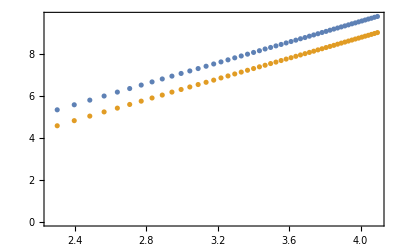

```mathematica
ListPlot[{{Log[nLst],Log[gTotalLst0]}ᵀ,{Log[nLst],Log[gTotalLst]}ᵀ},Frame->True,FrameLabel->xyLab,BaseStyle->texStyle,ImageSize->{Automatic,6cm}]
```

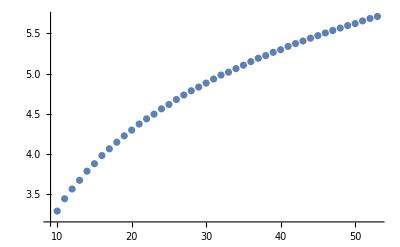

```mathematica
ListPlot[{nLst,Log[gRatioLst]}ᵀ]
```

```mathematica
gLst⟦pol,nBelow⟧
```

31.376

```mathematica
nRat
```

5.

```mathematica
n
```

11

```mathematica
ratio
```

0.4

```mathematica
n
```

11

```mathematica
nBelow
```

1

```mathematica
gLst⟦pol,nAbove⟧
```

10.786

```mathematica
fName
```

gDistilled_dim_3_N_60_param_divide_[80, 36, 36]_instanceNum_1000_seed_1000_alpha_0.2_alphaTest.npy

```mathematica
Total[gLst⟦1⟧]
```

232.925

## Read file from loops

```mathematica
fGMain="gDistilled";
fGVarMain="varG";
fDnMain="deltaN_distill";
fDnVarMain="deltaVar_distill";
fMod="";
```

```mathematica
itNum=1000;
seed=1000;
rat=0.4;
nDim=3;
div=80;
```

```mathematica
mSzLst=Table[n,{n,11,60}];
mSzNum=Length[mSzLst];
ratLst=Table[0.1ii,{ii,1,5}];
ratNum=Length[ratLst];
```

```mathematica
dCavgLst=ConstantArray[0,{mSzNum,ratNum}];
dCstdLst=ConstantArray[0,{mSzNum,ratNum}];
gAvgLst=ConstantArray[0,{mSzNum,ratNum}];
gStdLst=ConstantArray[0,{mSzNum,ratNum}];
```

```mathematica
resFun[40]
```

28

```mathematica
cAvgDivRat=1/4;
```

```mathematica
cDiv1=Floor[div cAvgDivRat];
cDiv2=Ceiling[div (1-cAvgDivRat)];
cDivNum=cDiv2-cDiv1+1;
```

```mathematica
{cDiv1,cDiv2}
```

{20,60}

```mathematica
{{1,2,3},{4,5,6}}//Dimensions
```

{2,3}

```mathematica
Mean[#]&/@{{1,2,3},{4,5,6}}
```

{2,5}

```mathematica
dCavgLstTmp//Dimensions
```

{59,80}

```mathematica
For[im=1,im≤mSzNum,im++,
mSz=mSzLst⟦im⟧;
res=resFun[mSz];
divLst={80,res,res};
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fNameDn=fNameFun[fDnMain,attrLst,valLst,fMod,npyType];
fNameDnVar=fNameFun[fDnVarMain,attrLstDim,valLstDim,fMod,npyType];
fNameG=fNameFun[fGMain,attrLstDim,valLstDim,fMod,npyType];
fNameGVar=fNameFun[fGVarMain,attrLstDim,valLstDim,fMod,npyType];
dCavgLstTmp=readPython[fNameDn];
dCstdLstTmp=readPython[fNameDnVar]⟦All,All,1⟧;
gLstTmp=readPython[fNameG]⟦1⟧;
gVarLstTmp=readPython[fNameGVar]⟦1⟧;
dCsatAvgTmp=Mean[#]&/@ dCavgLstTmp⟦All,cDiv1;;cDiv2⟧;
dCsatStdTmp=√((Mean[#]&)/@(( dCstdLstTmp⟦All,cDiv1;;cDiv2⟧)^2))/√cDivNum;
For[ir=1,ir≤ratNum,ir++,
rat=ratLst⟦ir⟧;
gAvgLst⟦im,ir⟧=aboveBelowAvg[gLstTmp,rat];
gStdLst⟦im,ir⟧=aboveBelowAvg[gVarLstTmp,rat,"isStd"->True];
dCavgLst⟦im,ir⟧=aboveBelowAvg[dCsatAvgTmp,rat];
dCstdLst⟦im,ir⟧=aboveBelowAvg[dCsatStdTmp,rat,"isStd"->True];
];
]
```

```mathematica
dCsatStdTmp
```

{0.845608,1.41039,1.92603,2.27242,2.56194,2.72824,3.00291,3.22726,3.41063,3.55047,3.84181,3.91319,4.13984,4.46686,4.50759,4.69652,4.67365,4.75708,4.90751,4.97983,5.14898,5.34145,5.35801,5.55972,5.47453,5.68518,5.82032,5.55403,5.93914,6.03915,5.94636,5.91419,5.75057,6.02251,5.98566,5.67697,6.10923,5.70387,5.38565,5.53706,5.62361,5.91521,5.37909,4.99941,5.23635,5.31877,4.93082,4.7299,4.67591,4.24926,4.24835,3.91577,3.83682,3.58414,3.28527,3.13504,2.72625,2.27164,1.68952}

```mathematica
dCstdLstTmp⟦20,All⟧
```

{10.9283,18.939,22.6153,23.284,24.6144,28.0474,28.8751,30.686,31.1602,29.6599,31.9741,30.044,31.3357,30.477,31.5761,29.6475,31.3198,31.4602,31.3093,30.378,32.2154,32.6505,34.352,33.2331,32.285,31.5561,31.5701,31.8208,30.8274,31.8316,31.3102,33.9299,34.3276,34.0422,33.0512,31.5977,30.6292,31.1344,29.7211,32.2599,32.0838,32.6916,32.4244,31.3615,32.0519,31.2268,31.3368,29.9139,31.7962,29.6336,29.2603,29.6674,32.4089,32.5755,33.8359,31.6401,33.1833,32.4522,30.2123,31.7982,34.0116,32.3531,32.2155,32.6987,32.1082,32.9224,29.8254,29.9769,32.1197,32.0386,30.1807,29.8541,29.4818,29.1843,29.7991,25.8222,22.2207,17.6551,10.721,0.960121}

```mathematica
dCavgLst⟦All,4⟧
```

{4.2486,4.70522,5.05021,5.36221,5.86175,6.16761,6.50927,6.8524,7.18072,7.69478,8.36616,8.44151,9.12416,9.46052,10.0636,10.2841,11.0566,10.998,11.6641,12.0296,12.427,12.9363,13.1964,14.0647,14.1315,14.6836,14.4829,15.3272,15.854,16.4642,16.5824,16.222,17.7215,17.8939,18.5281,18.9351,18.4706,19.6027,20.0155,20.7487,20.95,21.4061,21.6622,21.9462,23.0072,23.8785,23.8974,24.3504,23.6407,24.9142}

```mathematica
dCstdLst⟦All,4⟧
```

{4.25109,6.20014,5.45203,5.76175,7.51045,6.10396,8.30864,7.13701,7.75599,9.8154,8.36872,11.2285,9.78742,10.0344,12.6724,10.5135,14.1204,11.8282,12.6725,15.3092,12.3837,16.5026,14.3466,15.3305,17.8863,14.7253,18.9903,16.2709,16.7288,21.0089,16.6827,20.6003,19.129,19.4753,23.6246,18.8994,23.7379,21.4883,21.8266,26.7058,21.0703,27.8203,22.7333,24.052,29.875,23.9249,31.1367,25.947,25.8745,32.2308}

```mathematica
dCstdLstTmp//Dimensions
```

{59,80,1}

```mathematica
gLogStdLst=gStdLst/gAvgLst;
dCLogStdLst=dCstdLst/dCavgLst;
```

```mathematica
dCLogStdLst//Dimensions
```

{50,5}

```mathematica
dCsatAvgTmp//Dimensions
```

{59}

```mathematica
dCavgLst
```

{50,5}

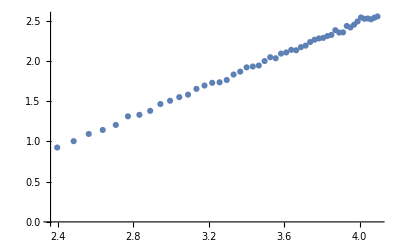

```mathematica
ListPlot[{Log[mSzLst],Log[dCavgLst⟦All,1⟧]}ᵀ]
```

```mathematica
gVarLstTmp//Dimensions
```

{59}

```mathematica
gStdLst⟦1⟧
```

{2.06864,2.61792,2.99806,3.26786,3.38394}

```mathematica
datGRatLst=Table[{Log[mSzLst],Log[gAvgLst⟦All,ir⟧]}ᵀ,{ir,1,ratNum}];
datGRatLstErr=Table[{Log[mSzLst],makeDataErr[Log[gAvgLst⟦All,ir⟧],gLogStdLst⟦All,ir⟧]}ᵀ,{ir,1,ratNum}];
datCRatLst=Table[{Log[mSzLst],Log[dCavgLst⟦All,ir⟧]}ᵀ,{ir,1,ratNum}];
datCRatLstErr=Table[{Log[mSzLst],makeDataErr[Log[dCavgLst⟦All,ir⟧],dCLogStdLst⟦All,ir⟧]}ᵀ,{ir,1,ratNum}];
```

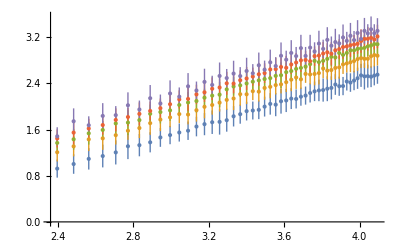

```mathematica
ListPlot[datCRatLstErr]
```

```mathematica
gFitModLst=Table[NonlinearModelFit[datGRatLst⟦ir⟧,r x+b,{r,b},{x},Weights->1/gLogStdLst⟦All,ir⟧^2,VarianceEstimatorFunction->(1&)],{ir,1,ratNum}];
```

```mathematica
gLiFitModLst=Table[LinearModelFit[datGRatLst⟦ir⟧,(x-Log[10]),x,Weights->1/gLogStdLst⟦All,ir⟧^2,VarianceEstimatorFunction->(1&)],{ir,1,ratNum}];
cLiFitModLst=Table[LinearModelFit[datCRatLst⟦ir⟧,(x-Log[10]),x,Weights->1/dCLogStdLst⟦All,ir⟧^2,VarianceEstimatorFunction->(1&)],{ir,1,ratNum}];
```

```mathematica
cFitFunLst=(#["Function"]&/@cLiFitModLst);
```

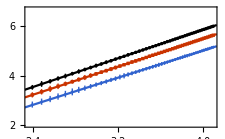

```mathematica
gFitFunLst=(#["Function"]&/@gLiFitModLst);pltGratErrFit=Show[ListPlot[datGRatLstErr⟦ratIdLst⟧,Frame->True,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotStyle->colorLst,BaseStyle->texStyle,ImageSize->8cm,FrameLabel->xyLabRatio,PlotRange->{Automatic, {2,6.7}}],Plot[Evaluate[#[x]&/@gFitFunLst⟦ratIdLst⟧],{x,Log[mSzLst⟦1⟧-2],Log[mSzLst⟦-1⟧+2]},PlotStyle->colorLst,PlotLegends->{Placed[LineLegend[legLstRat⟦ratIdLst⟧,LegendLabel->Placed[Column[{legLabRatLeft,""},Spacings->-0.8],Left],Spacings->0.5],Top],Placed[LineLegend[legLstSlope⟦ratIdLst⟧,LegendLabel->legLabSlope,Spacings->0.01],Scaled[{0.2,0.75}]]}],Graphics[Text[capTex⟦2⟧,Scaled[capLoc]]]]
```

```mathematica
gFitParamlst=(#["ParameterTableEntries"])&/@gLiFitModLst;
cFitParamlst=(#["ParameterTableEntries"])&/@cLiFitModLst;
```

```mathematica
gFitModLst⟦4⟧["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
r | 1.4618 | 0.0186224 | {1.42436,1.49924}
b | 0.0259383 | 0.0694521 | {-0.113705,0.165581}

```mathematica
gLiFitModLst⟦4⟧["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 3.39186 | 0.0270807 | {3.33741,3.44631}
x-Log[10] | 1.4618 | 0.0186224 | {1.42436,1.49924}

```mathematica
Exp[3.39]
```

29.666

```mathematica
Exp[3.39]/10^1.4618
```

1.02437

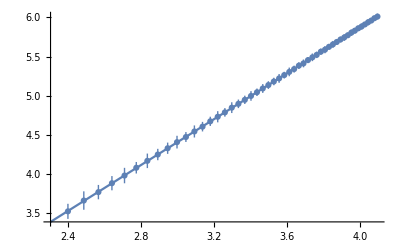

```mathematica
Show[Plot[gLiFitModLst⟦4⟧["Function"][x],{x,Log[10],Log[60]}],ListPlot[datGRatLstErr⟦4⟧]]
```

```mathematica
Exp[-0.1137]
```

0.892526

```mathematica
Exp[0.165581]
```

1.18008

```mathematica
Log[gAvgLst⟦All,4⟧]
```

{3.52651,3.66408,3.77147,3.88521,3.98271,4.08227,4.17041,4.25083,4.33101,4.40875,4.47398,4.54486,4.60608,4.67399,4.73234,4.78827,4.84832,4.89723,4.94802,4.99762,5.04475,5.09294,5.13636,5.18183,5.2213,5.26338,5.30411,5.33992,5.38419,5.41246,5.45477,5.49003,5.52122,5.56191,5.58766,5.62407,5.65502,5.6857,5.71709,5.74278,5.77142,5.80454,5.82977,5.85974,5.88289,5.9094,5.93697,5.95902,5.98856,6.0098}

```mathematica
gLogStdLst⟦All,4⟧
```

{0.0960994,0.117348,0.0916427,0.0906533,0.0983648,0.0735132,0.0924617,0.0726422,0.0717622,0.0808843,0.0631263,0.0768786,0.0610132,0.0588713,0.071191,0.0545419,0.068552,0.0545281,0.052955,0.0613419,0.0473629,0.0563119,0.0488968,0.0477423,0.0562056,0.0421662,0.0550705,0.0437976,0.0430497,0.0497301,0.0378535,0.0487566,0.040801,0.039653,0.0457408,0.0365355,0.0437919,0.0367381,0.0367156,0.0429765,0.0329827,0.0405645,0.0352755,0.0344115,0.0392537,0.0305083,0.0394593,0.0319559,0.0316555,0.0375749}

```mathematica
#[x]&/@gFitFunLst⟦ratIdLst⟧
```

{2.67455+1.38332 (x-Log[10]),3.08031+1.43002 (x-Log[10]),3.39186+1.4618 (x-Log[10])}

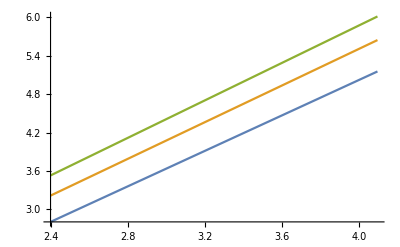

```mathematica
Plot[Evaluate[#[x]&/@gFitFunLst⟦ratIdLst⟧],{x,Log[mSzLst⟦1⟧],Log[mSzLst⟦-1⟧]},PlotStyle->Automatic]
```

```mathematica
ratIdLst={4,2,1};
```

```mathematica
legLabSlope=MaTeX["m= \\qquad \\quad",Magnification->labMag];
```

```mathematica
legLabRatLeft=MaTeX["n= \\,",Magnification->labMag];
```

```mathematica
legLabRatLeft
```

-Graphics-

```mathematica
pltGratErrFit=Show[ListPlot[datGRatLstErr⟦ratIdLst⟧,Frame->True,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotStyle->colorLst,BaseStyle->texStyle,ImageSize->8cm,FrameLabel->xyLabRatio,PlotRange->{Automatic, {2,6.7}}],Plot[Evaluate[#[x]&/@gFitFunLst⟦ratIdLst⟧],{x,Log[mSzLst⟦1⟧-2],Log[mSzLst⟦-1⟧+2]},PlotStyle->colorLst,PlotLegends->{Placed[LineLegend[legLstRat⟦ratIdLst⟧,LegendLabel->Placed[Column[{legLabRatLeft,""},Spacings->-0.8],Left],Spacings->0.5],Top],Placed[LineLegend[legLstSlope⟦ratIdLst⟧,LegendLabel->legLabSlope,Spacings->0.01],Scaled[{0.2,0.75}]]}],Graphics[Text[capTex⟦2⟧,Scaled[capLoc]]]]
```

-Graphics-

```mathematica
Export[fNameFun["gRatErrFit",{"ratio"},{ratLst},"",pdfType,True],pltGratErrFit]
```

gRatErrFit_ratio_0.1_0.2_0.3_0.4_0.5.pdf

```mathematica
legLstCSlope=MaTeX[ToString[NumberForm[#⟦2,1⟧,{2,1}]]<>"\\pm"<>ToString[NumberForm[#⟦2,2⟧,1]]]&/@cFitParamlst;
```

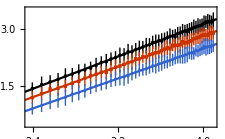

```mathematica
pltCratErrFit=Show[ListPlot[datCRatLstErr⟦ratIdLst⟧,Frame->True,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotStyle->colorLst,BaseStyle->texStyle,ImageSize->8cm,FrameLabel->CSumxyLab,PlotRange->{Automatic,{0.5,3.5}}],Plot[Evaluate[#[x]&/@cFitFunLst⟦ratIdLst⟧],{x,Log[mSzLst⟦1⟧-2],Log[mSzLst⟦-1⟧+2]},PlotStyle->colorLst,PlotLegends->{Placed[LineLegend[legLstCSlope⟦ratIdLst⟧,LegendLabel->legLabSlope,Spacings->0.01],Scaled[{0.2,0.75}]]}],Graphics[Text[capTex⟦3⟧,Scaled[capLoc]]]]
```

```mathematica
Export[fNameFun["cSatRatErrFit",{"ratio"},{ratLst⟦ratIdLst⟧},"",pdfType,True],pltCratErrFit]
```

cSatRatErrFit_ratio_0.4_0.2_0.1.pdf

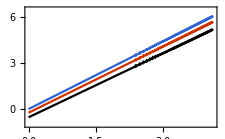

```mathematica
pltGratErrFit=Show[ListPlot[datGRatLstErr⟦ratIdLst⟧,Frame->True,PlotStyle->colorLst,BaseStyle->texStyle,ImageSize->8cm,FrameLabel->xyLabRatio,PlotRange->{{0,Log[mSzLst⟦-1⟧+2]},{-1,6.5}}],Plot[Evaluate[#[x]&/@gFitFunLst⟦ratIdLst⟧],{x,0,Log[mSzLst⟦-1⟧+2]},PlotStyle->colorLst,PlotLegends->LineLegend[legLstRat⟦ratIdLst⟧,LegendLabel->legLabRat,Spacings->Small],PlotRange->{{0,Log[mSzLst⟦-1⟧+2]},{-1,6.5}}],Axes->False]
```

```mathematica
ratLst
```

{0.1,0.2,0.3,0.4,0.5}

```mathematica
legLstRat=MaTeX[ToString[#]<>"M",Magnification->labMag]&/@ratLst;
```

```mathematica
legLstSlope=MaTeX[ToString[NumberForm[#⟦2,1⟧,{3,2}]]<>"\\pm"<>ToString[NumberForm[#⟦2,2⟧,{3,2}]]]&/@gFitParamlst;
```

```mathematica
legLstSlope
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
legLabRat=MaTeX["n= \\qquad\\quad",Magnification->labMag]
```

-Graphics-

```mathematica
legLstRat
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

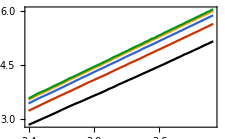

```mathematica
ListLinePlot[datGRatLst,BaseStyle->texStyle,Frame->True,PlotStyle->colorLst,PlotRangePadding->None,ImageSize->8cm,FrameLabel->xyLabRatio,PlotLegends->LineLegend[legLstRat,LegendLabel->legLabRat,Spacings->0.05]]
```

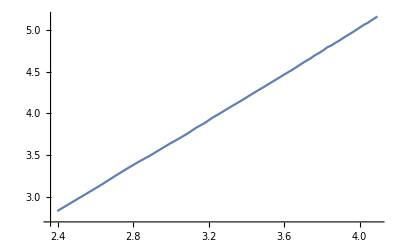

```mathematica
ListLinePlot[{Log[mSzLst],Log[gAvgLst⟦All,1⟧]}ᵀ]
```

```mathematica
fNameDn
```

deltaN_distill_N_60_param_divide_[80, 36, 36]_instanceNum_1000_seed_1000.npy

```mathematica
gLstTmp⟦30⟧
```

425.44

```mathematica
fBin[0.5]
```

0.980258

```mathematica
valLst
```

{60,{80,36,36},1000,1000}

```mathematica
gLstFull=readPython[fNameFun["gLst",attrLst,valLst,fMod,npyType]]⟦1⟧;
```

```mathematica
res=resFun[50];
res=16;
fMod="divBinplace";
gLstFull5016=readPython[fNameFun["gLst",attrLst,{50,{80,res,res},itNum,seed},fMod,npyType]]⟦1⟧;
```

```mathematica
fNameFun["gLst",attrLst,{50,{80,res,res},itNum,seed},fMod,npyType]
```

gLst_N_50_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_divBinplace.npy

```mathematica
gLstFull50//Dimensions
```

{50}

```mathematica
mSzLst1=Table[nn,{nn,30,60,2}];
numMSz1=Length[mSzLst1];
gMDatLst=ConstantArray[0,numMSz1];
```

```mathematica
fNameFun[fGMain,attrLst,valLst,fMod,npyType]
```

gDistilled_N_50_param_divide_[80, 32, 32]_instanceNum_1000_seed_1000.npy

```mathematica
valLst
```

{50,{80,32,32},1000,1000}

```mathematica
mSz
```

50

```mathematica
fMod="";
For[im=1,im≤numMSz1,im++,
mSz=mSzLst1⟦im⟧;
res=resFun[mSz];
divLst={80,res,res};
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
gLstTmp=readPython[fNameFun[fGMain,attrLstDim,valLstDim,fMod,npyType]]⟦1⟧;
gMDatLst⟦im⟧={Table[nn-0.5,{nn,1,mSz-1}]/(mSz-1),gLstTmp/Max[gLstTmp]}ᵀ;
]
```

```mathematica
gMDatLst⟦1⟧⟦All,2⟧
```

{0.143932,0.275312,0.38815,0.489404,0.57871,0.656971,0.729431,0.789923,0.842626,0.889735,0.926078,0.960096,0.97845,0.989592,1.,0.991164,0.981588,0.965696,0.932666,0.89796,0.852443,0.800591,0.740755,0.668523,0.590807,0.501572,0.40076,0.288007,0.156705}

```mathematica
xyLabG=MaTeX[#,Magnification->labMag]&/@{"\\frac{n-1/2}{M-1}",""};
```

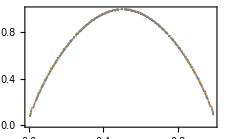

```mathematica
ListPlot[gMDatLst,Frame->True,ImageSize->8cm, BaseStyle->texStyle]
```

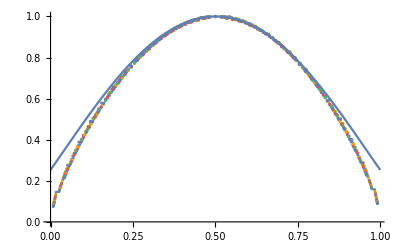

```mathematica
Show[ListPlot[gMDatLst],Plot[8(0.5^2-0.6(x-0.5)^2)^(3/2),{x,0,1}]]
```

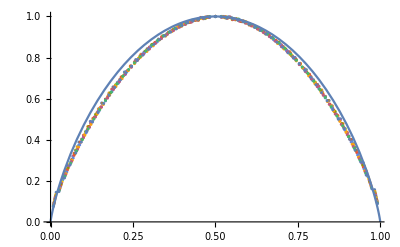

```mathematica
Show[ListPlot[gMDatLst],Plot[fBin[x],{x,0,1}]]
```

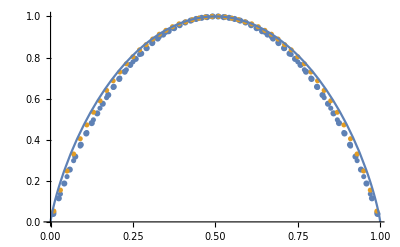

```mathematica
Show[ListPlot[{Table[n-0.5,{n,1,60}]/60,gLstFull/gLstFull⟦30⟧}ᵀ],ListPlot[{{Table[n-0.5,{n,1,50}]/50,gLstFull50/gLstFull50⟦25⟧}ᵀ,{Table[n-0.5,{n,1,50}]/50,gLstFull5016/gLstFull5016⟦25⟧}ᵀ}],Plot[fBin[x],{x,0,1}]]
```

```mathematica
gLstFull//Dimensions
```

{2,60}

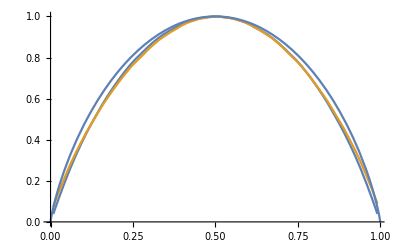

```mathematica
Show[ListLinePlot[{{Table[n-0.5,{n,1,60}]/60,gLstFull/Max[gLstFull]}ᵀ,{Table[n-0.5,{n,1,59}]/59,gLstTmp/Max[gLstTmp]}ᵀ}],Plot[fBin[x],{x,0,1}]]
```

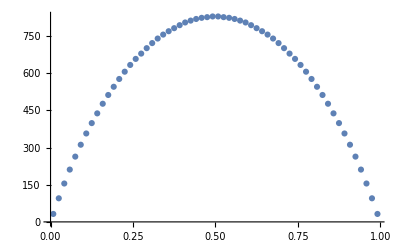

```mathematica
ListPlot[{Table[n-0.5,{n,1,60}]/60,gLstFull}ᵀ]
```

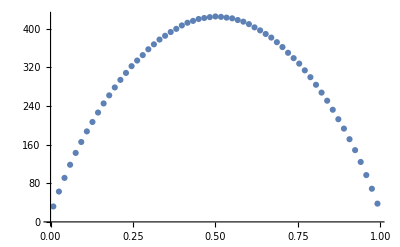

```mathematica
ListPlot[{Table[n-0.5,{n,1,59}]/59,gLstTmp}ᵀ]
```

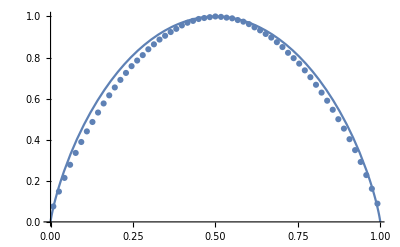

```mathematica
Show[ListPlot[{Table[n-0.5,{n,1,59}]/59,gLstTmp/gLstTmp⟦30⟧}ᵀ],Plot[fBin[x],{x,0,1}]]
```

```mathematica
gLstTmp//Dimensions
```

{59}

```mathematica
aboveBelowAvg[arr,11,0.4]
```

Part::partd: Part specification arr⟦5.⟧ is longer than depth of object.

arr⟦5.⟧

```mathematica
1
```

1

### No alpha

### Alphas

```mathematica
alpha=0.6;
alphaLst={0}~Join~Table[0.2ii,{ii,1,5}];
alphaLen=Length[alphaLst];
fNameMain="gDistilled";
fVarMain="varG";
fDnMain="deltaN_distill";
fDnVarMain="deltaVar_distill";
fModLst={""}~Join~ConstantArray["alphaTest",alphaLen-1];
itNum=200;
itNum0=1000;
itNumLst={1000}~Join~ConstantArray[200,alphaLen-1];
resMin=16;
resMax=32;
dRes=resMax-resMin;
nMin=10;
nMax=50;
dNres=nMax-nMin;
seed=1000;
dim=3;
div=80;
dNavgRat=1/4;
avgLbnd=Floor[div(1/2-dNavgRat)];
avgRbnd=Ceiling[div(1/2+dNavgRat)];
avgLen=avgRbnd-avgLbnd+1;
```

```mathematica
fModLst
```

{,alphaTest,alphaTest,alphaTest}

```mathematica
alphaLen
```

6

```mathematica
pol=1;
ratio=0.4;
```

```mathematica
nLst=Table[ii,{ii,10,60}];
gTotalLst=ConstantArray[0,{alphaLen,Length[nLst]}];
gTotalVarLst=ConstantArray[0,{alphaLen,Length[nLst]}];
gRatioLst=ConstantArray[0,{alphaLen,Length[nLst]}];
gRatioVarLst=ConstantArray[0,{alphaLen,Length[nLst]}];
dNRatioLst=ConstantArray[0,{alphaLen,Length[nLst]}];
dNRatioVarLst=ConstantArray[0,{alphaLen,Length[nLst]}];
attrLstNoDim={"N","param_divide","instanceNum","seed","alpha"};
attrLst={"dim"}~Join~attrLstNoDim;
```

```mathematica
dNLst//Dimensions
```

{59}

```mathematica
gTotalLst//Dimensions
```

{6,51}

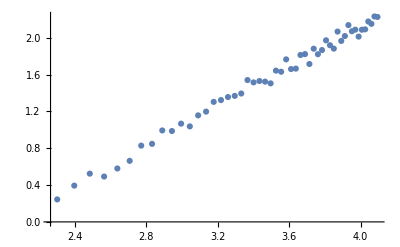

```mathematica
ListPlot[{Log[nLst],Log[dNRatioLst]}ᵀ]
```

```mathematica
wBelow dNLst⟦nBelow⟧+wAbove dNLst⟦nAbove⟧
```

9.25527

```mathematica
nAbove
```

25

```mathematica
valLstNoDim⟦1;;-2⟧
```

{60,{80,36,36},200,1000}

```mathematica
dNVarArr⟦1⟧
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

```mathematica
For[iA=1,iA≤alphaLen,iA++,
alpha=alphaLst⟦iA⟧;
For[iN=1,iN≤Length[nLst],iN++,
If[iA==1,attrCutId=-2,attrCutId=-1];
n=nLst⟦iN⟧;
res=16+Floor[(n-nMin)/dNres*dRes];
divArr={div,res,res};
itNum=itNumLst⟦iA⟧;
fMod=fModLst⟦iA⟧;
valLstNoDim={n,divArr,itNum,seed,NumberForm[alpha,{1,1}]};
valLst={dim}~Join~valLstNoDim;
fName=fNameFun[fNameMain,attrLst⟦1;;attrCutId⟧,valLst⟦1;;attrCutId⟧,fMod,npyType];
fVarName=fNameFun[fVarMain,attrLst⟦1;;attrCutId⟧,valLst⟦1;;attrCutId⟧,fMod,npyType];
fDnName=fNameFun[fDnMain,attrLstNoDim⟦1;;attrCutId⟧,valLstNoDim⟦1;;attrCutId⟧,fMod,npyType];
fDnVarName=fNameFun[fDnVarMain,attrLst⟦1;;attrCutId⟧,valLst⟦1;;attrCutId⟧,fMod,npyType];
gLst=readPython[fName];
gVarLst=readPython[fVarName];
dNArr=readPython[fDnName];
dNVarArr=readPython[fDnVarName];
dNLst=Mean[dNArrᵀ⟦avgLbnd;;avgRbnd,All⟧];
dNVarLst=√(Mean[dNVarArrᵀ⟦avgLbnd;;avgRbnd,All⟧^2]/avgLen);
gTotalLst⟦iA,iN⟧=Total[gLst⟦pol⟧];
gTotalVarLst⟦iA,iN⟧=√Total[gVarLst⟦pol⟧^2];
nRat=ratio(n-1)+1;
nAbove=Ceiling[nRat];
nBelow=Floor[nRat];
wBelow=(nAbove-nRat);
wAbove=(nRat-nBelow);
gRatioLst⟦iA,iN⟧=If[nAbove==nBelow , gLst⟦pol,nBelow⟧,wBelow gLst⟦pol,nBelow⟧+wAbove gLst⟦pol,nAbove⟧];
gRatioVarLst⟦iA,iN⟧=If[nAbove==nBelow , gVarLst⟦pol,nBelow⟧,√(wBelow^2 gVarLst⟦pol,nBelow⟧^2+wAbove^2 gVarLst⟦pol,nAbove⟧^2)];
dNRatioLst⟦iA,iN⟧=If[nAbove==nBelow , dNLst⟦nBelow⟧,wBelow dNLst⟦nBelow⟧+wAbove dNLst⟦nAbove⟧];
dNRatioVarLst⟦iA,iN⟧=If[nAbove==nBelow , dNVarLst⟦nBelow⟧,√(wBelow^2 dNVarLst⟦nBelow⟧^2+wAbove^2 dNVarLst⟦nAbove⟧^2)];
]]
```

```mathematica
dNRatioVarLstRe=ArrayReshape[dNRatioVarLst,{alphaLen,Length[nLst]}];
datLstLst={gTotalLst,gRatioLst,dNRatioLst};
varLstLst={gTotalVarLst,gRatioVarLst,dNRatioVarLstRe};
```

```mathematica
xyLab=MaTeX[#,Magnification->labMag]&/@{"\\log \\left( M \\right)","\\log \\langle N^{\\pm} \\rangle"};
xyLabRatio=MaTeX[#,Magnification->labMag]&/@{"\\log \\left( M \\right)","\\log \\langle N_n^{\\pm} \\rangle"};
CSumxyLab=MaTeX[#,Magnification->labMag]&/@{"\\log \\left( M \\right)","\\log \\langle \\left( \\Delta S_n \\right)^2 \\rangle_{\\rm sat}"};
```

```mathematica
xyLabLst={xyLab,xyLabRatio,CSumxyLab};
```

```mathematica
dNRatioVarLstRe=ArrayReshape[dNRatioVarLst,{alphaLen,Length[nLst]}];
```

```mathematica
dNRatioVarLst⟦1,1⟧
```

{4.68773}

```mathematica
dNRatioVarLstRe⟦1,1⟧
```

4.68773

```mathematica
dNVarLst⟦1,1⟧
```

0.

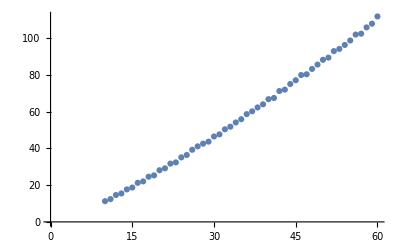

```mathematica
ListPlot[{nLst,varLstLst⟦1⟧⟦1,All⟧}ᵀ]
```

```mathematica
Length[datLstLst]
```

3

```mathematica
prossDatLst⟦1⟧⟦5⟧
```

{{Log[10],5.330.05},{Log[11],5.570.05},{Log[12],5.790.04},{Log[13],5.980.04},{Log[14],6.170.04},{Log[15],6.3370.033},{Log[16],6.5020.032},{Log[17],6.6530.028},{Log[18],6.7930.028},{Log[19],6.9270.025},{Log[20],7.0540.024},{Log[21],7.1730.022},{Log[22],7.2860.022},{Log[23],7.3970.020},{Log[24],7.5040.019},{Log[25],7.6030.018},{Log[26],7.7000.018},{Log[27],7.7960.017},{Log[28],7.8850.016},{Log[29],7.9710.015},{Log[30],8.0520.015},{Log[31],8.1350.014},{Log[32],8.2170.014},{Log[33],8.2900.013},{Log[34],8.3640.013},{Log[35],8.4330.012},{Log[36],8.5040.012},{Log[37],8.5710.011},{Log[38],8.6360.011},{Log[39],8.7030.011},{Log[40],8.7600.010},{Log[41],8.8250.010},{Log[42],8.8840.010},{Log[43],8.9420.009},{Log[44],9.0000.009},{Log[45],9.0520.009},{Log[46],9.1100.009},{Log[47],9.1630.008},{Log[48],9.2140.008},{Log[49],9.2650.008},{Log[50],9.3130.008},{Log[51],9.3620.008},{Log[52],9.4130.008},{Log[53],9.4560.007},{Log[54],9.5040.007},{Log[55],9.5480.007},{Log[56],9.5940.007},{Log[57],9.6380.007},{Log[58],9.6780.007},{Log[59],9.7230.006},{Log[60],9.7620.006}}

```mathematica
prossDatLst⟦1⟧⟦5⟧
```

{{Log[10],5.330.05},{Log[11],5.570.05},{Log[12],5.790.04},{Log[13],5.980.04},{Log[14],6.170.04},{Log[15],6.3370.033},{Log[16],6.5020.032},{Log[17],6.6530.028},{Log[18],6.7930.028},{Log[19],6.9270.025},{Log[20],7.0540.024},{Log[21],7.1730.022},{Log[22],7.2860.022},{Log[23],7.3970.020},{Log[24],7.5040.019},{Log[25],7.6030.018},{Log[26],7.7000.018},{Log[27],7.7960.017},{Log[28],7.8850.016},{Log[29],7.9710.015},{Log[30],8.0520.015},{Log[31],8.1350.014},{Log[32],8.2170.014},{Log[33],8.2900.013},{Log[34],8.3640.013},{Log[35],8.4330.012},{Log[36],8.5040.012},{Log[37],8.5710.011},{Log[38],8.6360.011},{Log[39],8.7030.011},{Log[40],8.7600.010},{Log[41],8.8250.010},{Log[42],8.8840.010},{Log[43],8.9420.009},{Log[44],9.0000.009},{Log[45],9.0520.009},{Log[46],9.1100.009},{Log[47],9.1630.008},{Log[48],9.2140.008},{Log[49],9.2650.008},{Log[50],9.3130.008},{Log[51],9.3620.008},{Log[52],9.4130.008},{Log[53],9.4560.007},{Log[54],9.5040.007},{Log[55],9.5480.007},{Log[56],9.5940.007},{Log[57],9.6380.007},{Log[58],9.6780.007},{Log[59],9.7230.006},{Log[60],9.7620.006}}

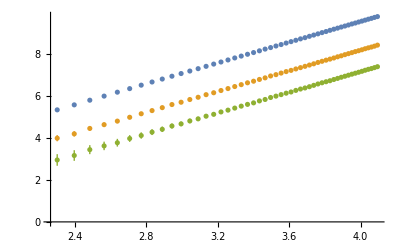

```mathematica
ListPlot[Table[prossDatLst⟦iA⟧⟦5⟧,{iA,1,alphaLen-1}]]
```

```mathematica
iD
```

1

```mathematica
prossDatLst=ConstantArray[0,alphaLen];
```

```mathematica
Length[datLstLst]-2
```

1

```mathematica
figW
```

141.732

```mathematica
prossDatLst⟦3⟧⟦5⟧
```

{{Log[10],1.00.6},{Log[11],1.20.7},{Log[12],1.40.4},{Log[13],1.40.5},{Log[14],1.50.5},{Log[15],1.630.34},{Log[16],1.70.5},{Log[17],1.80.4},{Log[18],1.90.4},{Log[19],1.980.32},{Log[20],2.090.28},{Log[21],2.10.4},{Log[22],2.180.27},{Log[23],2.280.27},{Log[24],2.300.29},{Log[25],2.400.23},{Log[26],2.460.29},{Log[27],2.460.24},{Log[28],2.550.24},{Log[29],2.620.23},{Log[30],2.640.21},{Log[31],2.660.28},{Log[32],2.700.22},{Log[33],2.790.23},{Log[34],2.810.22},{Log[35],2.860.19},{Log[36],2.860.23},{Log[37],2.900.18},{Log[38],2.960.20},{Log[39],3.010.19},{Log[40],3.050.16},{Log[41],3.060.23},{Log[42],3.120.16},{Log[43],3.160.19},{Log[44],3.180.18},{Log[45],3.220.16},{Log[46],3.220.21},{Log[47],3.280.14},{Log[48],3.290.17},{Log[49],3.350.18},{Log[50],3.350.13},{Log[51],3.390.18},{Log[52],3.440.13},{Log[53],3.450.15},{Log[54],3.480.15},{Log[55],3.500.12},{Log[56],3.540.20},{Log[57],3.570.11},{Log[58],3.590.13},{Log[59],3.610.14},{Log[60],3.630.12}}

```mathematica
varLstLst⟦3⟧⟦2,All⟧
```

{{1.4467},{2.27547},{1.82033},{1.87055},{2.17786},{2.20586},{3.33931},{2.47076},{3.40332},{3.33441},{3.00221},{4.24361},{3.43753},{3.97409},{4.09376},{3.8311},{5.69667},{4.04923},{4.79537},{5.64088},{4.73625},{6.66567},{4.77273},{5.02609},{6.14977},{5.23642},{8.1518},{5.39204},{6.19623},{7.29939},{6.5786},{7.63108},{6.85697},{7.16105},{7.63056},{7.07099},{9.15252},{7.04395},{9.27164},{8.62416},{7.59291},{11.5878},{8.14798},{9.49974},{8.84436},{8.20129},{11.8621},{8.81657},{9.82355},{11.0243},{9.36799}}

```mathematica
prossDatLst⟦2⟧⟦5⟧
```

{{Log[10],Log[1.27649{1.4467}]},{Log[11],Log[1.48268{2.27547}]},{Log[12],Log[1.68859{1.82033}]},{Log[13],Log[1.63632{1.87055}]},{Log[14],Log[1.78583{2.17786}]},{Log[15],Log[1.94022{2.20586}]},{Log[16],Log[2.2889{3.33931}]},{Log[17],Log[2.3332{2.47076}]},{Log[18],Log[2.69905{3.40332}]},{Log[19],Log[2.68224{3.33441}]},{Log[20],Log[2.90556{3.00221}]},{Log[21],Log[2.82061{4.24361}]},{Log[22],Log[3.17829{3.43753}]},{Log[23],Log[3.31122{3.97409}]},{Log[24],Log[3.68066{4.09376}]},{Log[25],Log[3.75278{3.8311}]},{Log[26],Log[3.87866{5.69667}]},{Log[27],Log[3.92778{4.04923}]},{Log[28],Log[4.03037{4.79537}]},{Log[29],Log[4.66415{5.64088}]},{Log[30],Log[4.54763{4.73625}]},{Log[31],Log[4.61585{6.66567}]},{Log[32],Log[4.58471{4.77273}]},{Log[33],Log[4.49971{5.02609}]},{Log[34],Log[5.16705{6.14977}]},{Log[35],Log[5.1041{5.23642}]},{Log[36],Log[5.83768{8.1518}]},{Log[37],Log[5.25551{5.39204}]},{Log[38],Log[5.28071{6.19623}]},{Log[39],Log[6.12376{7.29939}]},{Log[40],Log[6.18188{6.5786}]},{Log[41],Log[5.55085{7.63108}]},{Log[42],Log[6.55402{6.85697}]},{Log[43],Log[6.17461{7.16105}]},{Log[44],Log[6.45968{7.63056}]},{Log[45],Log[7.18007{7.07099}]},{Log[46],Log[6.80878{9.15252}]},{Log[47],Log[6.56176{7.04395}]},{Log[48],Log[7.8961{9.27164}]},{Log[49],Log[7.13095{8.62416}]},{Log[50],Log[7.52051{7.59291}]},{Log[51],Log[8.46732{11.5878}]},{Log[52],Log[7.92337{8.14798}]},{Log[53],Log[8.05963{9.49974}]},{Log[54],Log[7.47507{8.84436}]},{Log[55],Log[8.05527{8.20129}]},{Log[56],Log[8.08793{11.8621}]},{Log[57],Log[8.8068{8.81657}]},{Log[58],Log[8.58617{9.82355}]},{Log[59],Log[9.30234{11.0243}]},{Log[60],Log[9.25527{9.36799}]}}

```mathematica
ListPlot[prossDatLst⟦1⟧⟦5⟧,PlotRange->All]
```

-Graphics-

```mathematica
ToString[2]
```

2

```mathematica
ToString[NumberForm[prossDatLst⟦1⟧⟦8⟧,pres]]
```

2.47

```mathematica
legLab=MaTeX["m=\\hspace{1.2cm}",Magnification->labMag];
```

```mathematica
legLab
```

-Graphics-

```mathematica
pltLstAlphaSc=ConstantArray[0,Length[datLstLst]];
```

```mathematica
imgPad={{50,10},{30,10}};
```

```mathematica
figW=11cm;figH=7cm;
aspRat=figH/(figW-imgPad⟦1,2⟧);
pres=3;presErr=1;
```

```mathematica
Rationalize[141.73228346456693]
```

18000/127

```mathematica
tt=LineLegend[colorLst⟦1;;alphaLen-1⟧,Table[MaTeX[ToString[NumberForm[prossDatLst⟦iA⟧⟦8⟧,pres]]<>"\\pm "<>ToString[NumberForm[prossDatLst⟦iA⟧⟦9⟧,presErr]]],{iA,1,alphaLen-1}],LegendLabel->Placed[legLab,Top],Spacings->0.2]
```

```mathematica
Head[tt]
```

LineLegend

```mathematica
bl=BarLegend["Rainbow",LegendLabel->Placed["foo",Above],LegendFunction->lgPadFun]
```

```mathematica
lgPadFun[bl]
```

Show::shx: No graphical objects to show.

Show[{},ImagePadding→{{Automatic,30},{Automatic,Automatic}}]

```mathematica
Cases[bl,_Graphics,All]
```

{}

```mathematica
Row[BarLegend["Rainbow",LegendLabel->Placed["foo",#],LegendFunction->lgPadFun]&/@{Above,Below}]
```

```mathematica
cm
```

28.3465

```mathematica
lgPadFun2=Show[#,ImagePadding->{{Automatic,10},{Automatic,Automatic}}]&;
```

```mathematica
lgPadFun=Show[Cases[#,_Graphics,All],ImagePadding->{{Automatic,30},{Automatic,Automatic}}]&;
```

```mathematica
prossDatLst=ConstantArray[0,alphaLen];
```

```mathematica
iA
```

6

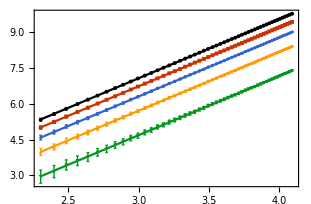

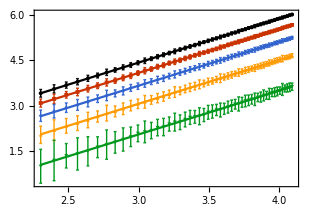

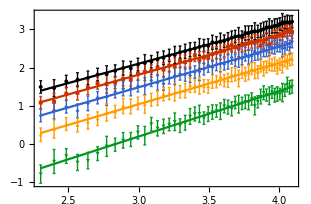

```mathematica
capLoc={0.07,0.9};
For[iD=1,iD≤Length[datLstLst],iD++,
For[iA=1,iA≤alphaLen-1,iA++,
prossDatLst⟦iA⟧=processFun[datLstLst⟦iD⟧⟦iA,All⟧,varLstLst⟦iD⟧⟦iA,All⟧,nLst];
];
Print[pltLstAlphaSc⟦iD⟧=Show[Plot[Evaluate[Table[prossDatLst⟦iA⟧⟦6⟧[nn],{iA,1,alphaLen-1}]],{nn,Log[Min[nLst]],Log[Max[nLst]]},PlotStyle->colorLst,(*PlotLegends->Placed[LineLegend[Table[MaTeX[ToString[NumberForm[prossDatLst⟦iA⟧⟦8⟧,pres]]<>"\\pm "<>ToString[NumberForm[prossDatLst⟦iA⟧⟦9⟧,presErr]]],{iA,1,alphaLen-1}],LegendLabel->Placed[legLab,Top],Spacings->0.2],{1,0.7}],*)Frame->True,FrameLabel->xyLabLst⟦iD⟧,ImageSize->{figW,figH},ImagePadding->imgPad,AspectRatio->aspRat],ListPlot[Table[prossDatLst⟦iA⟧⟦5⟧,{iA,1,alphaLen-1}],PlotMarkers->{Automatic,AbsolutePointSize[4]},PlotStyle->colorLst,BaseStyle->texStyle,Frame->True,IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->fenceW/2|>,PlotRange->Full],Graphics[Text[capTex⟦iD+1⟧,Scaled[capLoc]]],Axes->False,BaseStyle->texStyle,PlotRange->All]]]
```

```mathematica
pltLstAlphaSc⟦1⟧⟦2,2⟧
```

{1,0.7}

```mathematica
pltLstAlphaScGd=pltLstAlphaSc;
```

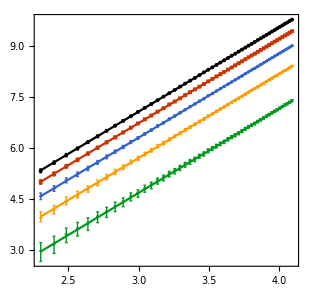
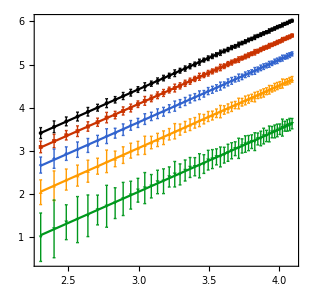
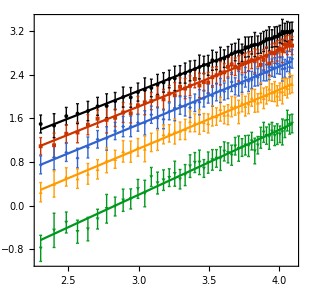

```mathematica
pltLstAlphaScGd=Show[#⟦1⟧,Graphics[Inset[#⟦2,1⟧,Scaled[{1.3,0.65}]]],PlotRangeClipping->False]&/@pltLstAlphaSc
```

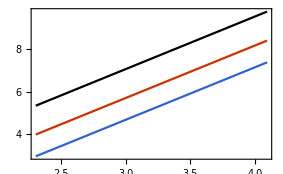

```mathematica
Show[makeInset[pltLstAlphaSc⟦1⟧],PlotRangeClipping->False]
```

```mathematica
Show[Placed[,Top]]
```

Show::gtype: Placed is not a type of graphics.

Show[Placed[Circle[{0,0}],Top]]

```mathematica
legLabAlpha=MaTeX["\\hspace{1cm}\\vspace*{-0.5cm}\\alpha = \\\\",Magnification->labMag];
```

```mathematica
legLabAlpha
```

-Graphics-

```mathematica
Column[{legLabAlpha,""},Spacings->-0.5]
```

-Graphics-

```mathematica
Information[LineLegend]
```

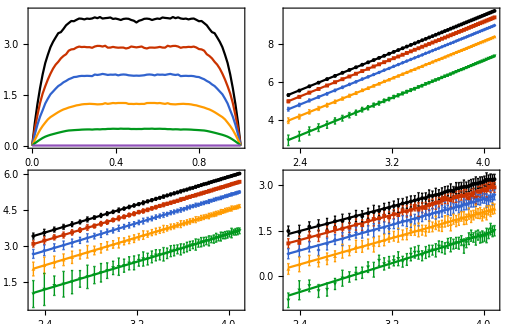

```mathematica
pltAlphaScGrd=Show[Legended[GraphicsGrid[{{dNplt,pltLstAlphaScGd⟦1⟧},{pltLstAlphaScGd⟦2⟧,pltLstAlphaScGd⟦3⟧}},ImageSize->{18cm,Automatic},Alignment->{Left,Top},Spacings->Scaled[0.00],AspectRatio->figH/figW],Placed[LineLegend[colorLst,legLst,LegendLabel->Placed[Column[{legLabAlpha,""},Spacings->-0.8],Left],LegendLayout->{"Row",1}],Below]]]
```

```mathematica
Export["dNandScaling_alphas.eps",pltAlphaScGrd];
```

```mathematica
Grid[{{legLabAlpha},{Style["a",3]}}]
```

-Graphics-
a

```mathematica
Rotate[Style["a=1",10,Red],90 Degree]
```

a=1

```mathematica
Translate[Text[Style["a=1"]],{0,1}]
```

Translate[a=1,{0,1}]

```mathematica
Head["a=1"]
```

String

```mathematica
Rotate["a=1",90Degree]
```

a=1

```mathematica
LineLegend[colorLst,legLst,LegendLabel->Placed[legLabAlpha,Left],LegendLayout->{"Row",1},LegendMargins->{{0,0},{0,0}}]
```

```mathematica
Graphics[Translate[Style["a=1",10,Red],{0,1}],Axes->True]
```

-Graphics-

```mathematica
Translate[Style["a=1",10,Red],{0,1}]
```

Translate[a=1,{0,1}]

```mathematica
prossDatLst⟦3⟧⟦6⟧
```

NonlinearModelFit::wts: The value of option Weights -> {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«41»} should be a list of real numbers or a pure function.

Part::partd: Part specification «1» is longer than depth of object.

FittedModel[-3.36496+1.18702 x]

```mathematica
Table[prossDatLst⟦iA⟧⟦6⟧[n],{iA,1,alphaLen-1}]
```

NonlinearModelFit::wts: The value of option Weights -> {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«41»} should be a list of real numbers or a pure function.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::wts: The value of option Weights -> {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«41»} should be a list of real numbers or a pure function.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«41»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

{59.7042,62.5458,67.8561}

NonlinearModelFit::wts: The value of option Weights -> {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«41»} should be a list of real numbers or a pure function.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::wts: The value of option Weights -> {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«41»} should be a list of real numbers or a pure function.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«41»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

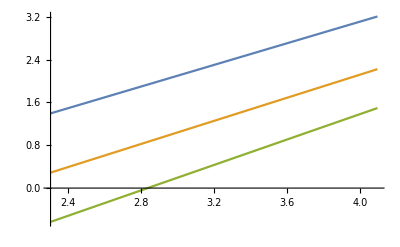

```mathematica
Plot[Evaluate[Table[prossDatLst⟦iA⟧⟦6⟧[nn],{iA,1,alphaLen-1}]],{nn,Log[Min[nLst]],Log[Max[nLst]]}]
```

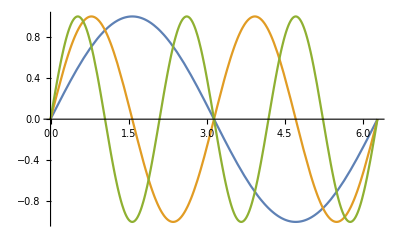

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 Pi}]
```

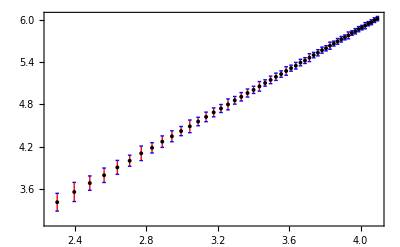

```mathematica
ListPlot[prossDatLst⟦1⟧⟦5⟧,PlotStyle->Black,IntervalMarkers->"Fences",IntervalMarkersStyle-><|"WhiskerStyle"->Red,"FenceWidth"->fenceW/2,"FenceStyle"->Blue|>,PlotMarkers->{Automatic,AbsolutePointSize[4]},BaseStyle->texStyle,ImageSize->{Automatic,figW},Frame->True,FrameLabel->xyLab]
```

```mathematica
MaTeX["a+c",Magnification->labMag]
```

-Graphics-

```mathematica
gTotalLst0=ConstantArray[0,Length[nLst]];
gRatioLst0=ConstantArray[0,Length[nLst]];
attrLst={"dim","N","param_divide","instanceNum","seed"};
fMod="";
For[iN=1,iN≤Length[nLst],iN++,
n=nLst⟦iN⟧;
res=16+Floor[(n-nMin)/dNres*dRes];
divArr={80,res,res};
valLst={dim,n,divArr,If[n==10,5000,itNum],seed};
fName=fNameFun[fNameMain,attrLst,valLst,fMod,npyType];
gLst=readPython[fName];
gTotalLst0⟦iN⟧=Total[gLst⟦pol⟧];
nRat=ratio(n-1)+1;
nAbove=Ceiling[nRat];
nBelow=Floor[nRat];
gRatioLst0⟦iN⟧=If[nAbove==nBelow , gLst⟦pol,nBelow⟧,(nAbove-nRat)gLst⟦pol,nBelow⟧+(nRat-nBelow)gLst⟦pol,nAbove⟧];
]
```

```mathematica
gRatioLst
```

{26.9084,31.376,35.4116,39.447,44.1744,48.4606,53.643,58.3218,63.322,68.5514,73.589,79.338,84.6682,89.7258,95.8592,101.161,107.643,113.811,119.966,125.566,131.981,138.766,145.804,151.088,157.964,164.824,172.301,179.717,185.723,193.419,199.76,208.246,215.577,222.58,230.533,237.979,245.902,253.46,261.432,269.623,276.415,285.715,294.549,301.966}

```mathematica
fName
```

gDistilled_dim_3_N_60_param_divide_[80, 36, 36]_instanceNum_200_seed_1000_alpha_0.6_alphaTest.npy

```mathematica
gLst=readPython[fName];
```

ExternalEvaluate::invalidSession: The session … is invalid and cannot be used.

```mathematica
gTotalLst
```

{96.344,122.829,152.503,186.123,222.795,265.222,310.434,360.806,414.63,477.473,540.444,609.049,683.531,760.609,842.711,935.948,1028.28,1130.76,1234.6,1347.02,1462.72,1585.67,1710.13,1853.06,1985.52,2139.72,2291.18,2445.69,2614.54,2786.8,2966.87,3147.,3335.22,3544.63,3744.56,3964.07,4179.73,4401.58,4649.6,4893.34,5139.18,5396.32,5660.68,5940.14,6209.62,6501.46,6803.2,7090.88,7406.5,7726.82,8072.49}

```mathematica
gTotalLst0
```

{205.565,261.152,326.006,396.008,477.321,565.171,666.349,774.761,891.377,1019.59,1157.54,1304.06,1460.,1630.91,1816.18,2004.36,2209.29,2430.32,2656.63,2895.81,3141.14,3411.36,3703.88,3982.05,4290.3,4594.28,4932.41,5278.72,5631.05,6020.34,6375.21,6802.55,7218.5,7643.35,8106.16,8538.16,9042.07,9536.66,10032.6,10562.8,11085.7,11642.,12241.7,12786.9}

```mathematica
{{1,2,3},{4,5,6}}^2
```

{{1,4,9},{16,25,36}}

```mathematica
divArr={80,16,16};n=10;
```

```mathematica
valLstNoDim={n,divArr,If[n==10,5000,itNum],seed,alpha};
```

```mathematica
fDnName=fNameFun[fDnMain,attrLstNoDim,valLstNoDim,fMod,npyType];
```

```mathematica
fDnName
```

deltaN_distill_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000_alpha_0.6_alphaTest.npy

```mathematica
dNArr=readPython[fDnName];
```

ExternalEvaluate::invalidSession: The session … is invalid and cannot be used.

```mathematica
dNArr//Dimensions
```

{9,80}

```mathematica
alpha=0.6;
```

```mathematica
attrLst
```

{dim,N,param_divide,instanceNum,seed,alpha}

```mathematica
div
```

80

```mathematica
valLst={dim,n,divArr,If[n==10,5000,itNum],seed};
```

```mathematica
attrLst={"N","param_divide","instanceNum","seed","alpha"};
```

```mathematica
fName=fNameFun["deg",attrLst,valLst,fMod,jld2Type];
```

```mathematica
fName
```

deg_dim_3_N_11_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_alpha_0.2_alphaTest.jld2

```mathematica
fName
```

```mathematica
ListPlot[{{Log[nLst],Log[gTotalLst0]}ᵀ,{Log[nLst],Log[gTotalLst]}ᵀ},Frame->True,FrameLabel->xyLab,BaseStyle->texStyle,ImageSize->{Automatic,6cm}]
```

-Graphics-

```mathematica
ListPlot[{nLst,Log[gRatioLst]}ᵀ]
```

-Graphics-

```mathematica
gLst⟦pol,nBelow⟧
```

31.376

```mathematica
nRat
```

5.

```mathematica
n
```

11

```mathematica
ratio
```

0.4

```mathematica
n
```

11

```mathematica
nBelow
```

1

```mathematica
gLst⟦pol,nAbove⟧
```

10.786

```mathematica
fName
```

gDistilled_dim_3_N_60_param_divide_[80, 36, 36]_instanceNum_1000_seed_1000_alpha_0.2_alphaTest.npy

```mathematica
Total[gLst⟦1⟧]
```

232.925

```mathematica
figW/cm
```

5.

```mathematica
testFit=NonlinearModelFit[{{1,1},{2,2.1},{3,2.9}},a x+b,{a,b},{x},VarianceEstimatorFunction->(1&),Weights->0.1/{0.1,0.1,0.3}^2]
```

FittedModel[-0.0142857+1.03571 x]

```mathematica
testFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.03571 | 0.368394 | 2.81143 | 0.217556
b | -0.0142857 | 0.621059 | -0.0230022 | 0.985359

```mathematica
Clear[x]
```

## Processing

```mathematica
processFun[dataLst_,varLst_,xLst_]:=Module[{varLogLst,ln,dataLstErr,logLstErr,dataLog,dataLogErr,fitMod,fitEntries,powLog,powLogErr},
varLogLst=varLst/dataLst;
ln=Length[xLst];
dataLstErr=makeDataErr[dataLst,varLst];
logLstErr=makeDataErr[Log[dataLst],varLogLst];
dataLog={Log[xLst],Log[dataLst]}ᵀ;
dataLogErr={Log[xLst],Log[dataLstErr]}ᵀ;
fitMod=NonlinearModelFit[dataLog,r x +b,{r,b},{x},Weights->1/varLogLst^2,VarianceEstimatorFunction->(1&)];
fitEntries=fitMod["ParameterTableEntries"];
powLog=fitEntries⟦1,1⟧;
powLogErr=fitEntries⟦1,2⟧;
{varLogLst,dataLstErr,logLstErr,dataLog,dataLogErr,fitMod,fitEntries,powLog,powLogErr}
]
```

```mathematica
{gVarLogLst,gTotalLstErr,gLogLstErr,dataLog,dataLogErr,logFitMod,logFitEntries,powLog,powLogErr}=processFun[gTotalLst,gVarLst,Nlst];
```

```mathematica
{gRatioVarLogLst,gRatioLstErr,gRatioLogLstErr,dataRatioLog,dataRatioLogErr,logFitModRatio,logFitEntriesRatio,powLogRatio,powLogErrRatio}=processFun[gRatioLst,gRatioVarLst,NRatiolst];
```

```mathematica
logFitEntries
```

{{2.46263,0.0512411,48.0597,2.97331×10^-42},{0.358092,0.189919,1.8855,0.0654223}}

```mathematica
gTotLinFit=LinearModelFit[dataLog,(x-Log[10]),x,VarianceEstimatorFunction->(1&),Weights->gVarLogLst]
```

FittedModel[6.04217+2.45026 (x-Log[10])]

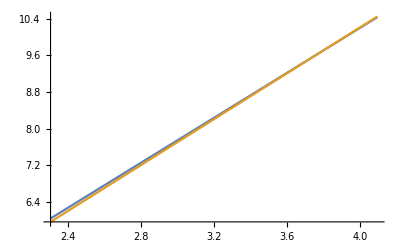

```mathematica
Plot[{gTotLinFit[x],Log[cst]+2.5x},{x,Log[10],Log[60]}]
```

```mathematica
Exp[6.04]
```

419.893

```mathematica
cstOurs=Exp[6.04]/10^2.45
```

1.48984

```mathematica
cst//N
```

1.23538

```mathematica
cstOurs/cst
```

1.20597

```mathematica
Exp[6.04]/10^2.45
```

```mathematica
logFitEntriesRatio
```

{{1.46097,0.0662184,22.0628,8.96237×10^-27},{0.695302,0.240297,2.89351,0.00571361}}

```mathematica
√2 fBin[0.4]
```

1.34602

```mathematica
Exp[0.5-4]
```

0.0301974

```mathematica
Nlst
```

{11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}

```mathematica
gRatioLst
```

{65.3028,75.1312,84.2726,94.289,104.851,115.217,125.984,137.564,148.017,161.007,171.976,183.069,196.338,209.032,222.703,234.601,248.047,261.859,274.265,289.843,302.448,316.39,332.278,346.302,363.148,376.305,390.453,407.125,423.142,439.287,455.198,469.828,487.396,505.089,522.145,538.485,554.381,573.822,590.842,609.751,624.173,642.106,662.371,680.221,700.25,716.843,734.468,754.824,774.252,794.274}

```mathematica
M=20;
{gTotalLst⟦M-10⟧,gVarLst⟦M-10⟧}
```

{2387.84,85.8613}

```mathematica
0.358092
```

```mathematica
Log[2]//N
```

0.693147

```mathematica
Mtmp=10
```

10

```mathematica
gTotalLst⟦10⟧
```

2387.84

```mathematica
2387.84/2209.92
```

1.08051

```mathematica
420/390//N
```

1.07692

```mathematica
cst Mtmp^(5/2)//N
```

390.662

```mathematica
gTotalLst⟦40⟧
```

21904.2

```mathematica
21904.2/21838.6
```

1.003

```mathematica
c1=Exp[logFitEntries⟦2,1⟧]
```

1.4306

```mathematica
c2=Exp[logFitEntriesRatio⟦2,1⟧]
```

2.00431

```mathematica
c2/c1
```

1.40103

```mathematica
fitTotRat=NonlinearModelFit[{Log[Nlst],Log[gTotalLst/gRatioLst]}ᵀ,r x+b,{r,b},{x}]
```

FittedModel[-0.312492+0.994652 x]

```mathematica
fitTotRat["ParameterTableEntries"]
```

{{0.994652,0.0047926,207.539,1.50195×10^-72},{-0.312492,0.0167841,-18.6183,1.33965×10^-23}}

```mathematica
Exp[-fitTotRat["ParameterTableEntries"]⟦2,1⟧]
```

1.36683

```mathematica
√2 fBin[0.4]//N
```

1.34602

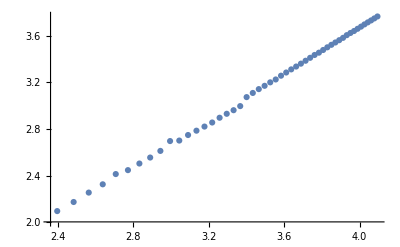

```mathematica
ListPlot[{Log[Nlst],Log[gTotalLst/gRatioLst]}ᵀ]
```

```mathematica
c1 √2 fBin[0.5]
```

1.98323

```mathematica
cst//N
```

1.23538

```mathematica
cst=512/(135 √(3π));
```

```mathematica
Log[cst]//N
```

0.211379

```mathematica
testFun[]:={1,2,3};
```

```mathematica
{a,b,c}=testFun[]
```

{1,2,3}

```mathematica
gVarLogLst=gVarLst/gTotalLst;
```

```mathematica
gLn=Length[Nlst];
```

```mathematica
gTotalLstErr=Table[Around[gTotalLst⟦it⟧,gVarLst⟦it⟧],{it,1,gLn}];
```

```mathematica
gLogLstErr=Table[Around[Log[gTotalLst⟦it⟧],gVarLogLst⟦it⟧],{it,1,gLn}];
```

```mathematica
dataLogErr={Log[Nlst],gLogLstErr}ᵀ;
```

```mathematica
dataLog={Log[Nlst],Log[gTotalLst]}ᵀ;
```

```mathematica
NlstEven
```

{10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60}

## Test

-9+ⅇ

```mathematica
gTotalLst
```

{182.955,232.925,289.471,351.813,424.119,502.48,590.175,686.813,787.257,905.311,1024.03,1157.59,1296.68,1444.75,1604.53,1772.62,1951.43,2150.16,2342.94,2558.01,2781.9,3016.68,3269.11,3519.97,3783.97,4064.32,4362.13,4676.55,4970.74,5313.16,5643.48,6007.77,6381.91,6754.21,7154.63,7544.39,7979.42,8417.27,8851.97,9335.53,9782.43,10292.1,10812.1,11311.6}

```mathematica
{gVarLogLst,gTotalLstErr,gLogLstErr,dataLog,dataLogErr,logFitMod,logFitEntries,powLog,powLogErr}=processFun[gTotalLst,ConstantArray[10^-9,Length[gTotalLst]],nLst];
```

```mathematica
{gVarLogLst0,gTotalLstErr0,gLogLstErr0,dataLog0,dataLogErr0,logFitMod0,logFitEntries0,powLog0,powLogErr0}=processFun[gTotalLst0,ConstantArray[10^-9,Length[gTotalLst0]],nLst];
```

```mathematica
logFitLab0=MaTeX[#,Magnification->1]&/@{"m="<>ToString[NumberForm[powLog0,pres]]}
```

{-Graphics-}

```mathematica
logFitMod
```

FittedModel[-0.456286+2.46585 x]

```mathematica
logFitMod0
```

FittedModel[-0.342781+2.4686 x]

```mathematica
logFitLab=MaTeX[#,Magnification->1]&/@{"m="<>ToString[NumberForm[powLog,pres]]}
```

{-Graphics-}

```mathematica
labAl0=MaTeX[#,Magnification->1]&/@{"\\alpha=0"};
labAl01=MaTeX[#,Magnification->1]&/@{"\\alpha=0.4"};
```

```mathematica
labAl0
```

{-Graphics-}

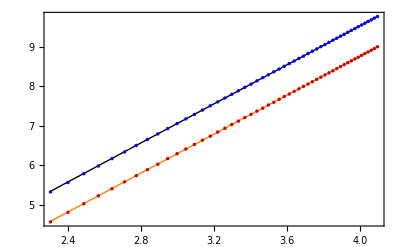

```mathematica
Show[{Plot[logFitMod[x],{x,Min[Log[nLst]],Max[Log[nLst]]},PlotStyle->{Orange,dataThick},PlotLegends->Placed[LineLegend[logFitLab],{{legX-0.04,0.88},Right}]],ListPlot[{Log[nLst],Log[gTotalLst]}ᵀ,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotStyle->darkRed,PlotLegends->Placed[LineLegend[labAl01],{{legX,0.75},Right}]],
Plot[logFitMod0[x],{x,Min[Log[nLst]],Max[Log[nLst]]},PlotStyle->{Black,dataThick},PlotLegends->Placed[LineLegend[logFitLab0],{{legX-0.04,0.62},Right}]],ListPlot[{Log[nLst],Log[gTotalLst0]}ᵀ,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotStyle->Blue,PlotLegends->Placed[LineLegend[labAl0],{{legX,0.49},Right}]]},PlotRange->All,FrameLabel->xyLab,Frame->True,BaseStyle->texStyle,ImageSize->{Automatic,figW}]
```

## Cmax

```mathematica
Length[Nlst]
```

50

```mathematica
CmaxLst
```

CmaxLst

```mathematica
CmaxLstEven//Dimensions
```

{26}

```mathematica
NlstEven//Dimensions
```

{26}

```mathematica
{CarLogLstEven,CLstErrEven,CLogLstErrEven,CdataLogEven,CdataLogErrEven,CFitModEven,CFitEntriesEven,CpowLogEven,CpowLogErrEven}=processFun[CmaxLstEven,CvarLstEven,NlstEven];
```

```mathematica
{CarLogLst04,CLstErr04,CLogLstErr04,CdataLog04,CdataLogErr04,CFitMod04,CFitEntries04,CpowLog04,CpowLogErr04}=processFun[CmaxLst04,CvarLst04,NlstC04];
```

```mathematica
CvarLst04
```

{0.08399,0.0968325,0.0885529,0.10096,0.104975,0.104447,0.140678,0.107491,0.13508,0.133169,0.134353,0.182084,0.141168,0.173187,0.169153,0.164449,0.233124,0.178524,0.21851,0.217977,0.193105,0.281995,0.210218,0.236192,0.261709,0.228098,0.325369,0.239093,0.278913,0.285321,0.266822,0.379831,0.264884,0.333537,0.349442,0.304635,0.4438,0.304769,0.365531,0.379471,0.345036,0.480424,0.341539,0.411139,0.426338,0.370046,0.555859,0.388514,0.46031,0.437666,0.406055}

```mathematica
NonlinearModelFit[CmaxLstEven,r x +b,{r,b},{x},Weights->1/(CvarLstEven/CmaxLstEven),VarianceEstimatorFunction->(1&)]
```

FittedModel[6.56602+1.39775 x]

## Fit

```mathematica
logFit=NonlinearModelFit[dataLog,r x+b,{r,b},{x},Weights->1/(gVarLogLst)^2,VarianceEstimatorFunction->(1&)]
```

FittedModel[0.347459+2.4655 x]

```mathematica
logFitRatio=NonlinearModelFit[dataRatioLog,r x+b,{r,b},{x},Weights->1/(gRatioVarLogLst)^2,VarianceEstimatorFunction->(1&)]
```

FittedModel[0.699165+1.45988 x]

```mathematica
logFit[{"BestFit","ParameterTable"}]
```

{0.347459+2.4655 x, | Estimate | Standard Error | t-Statistic | P-Value
r | 2.4655 | 0.00833771 | 295.705 | 6.33949×10^-80
b | 0.347459 | 0.0318961 | 10.8935 | 1.42793×10^-14}

```mathematica
logFitConfEntries=logFit["ParameterConfidenceIntervalTableEntries"]
```

{{2.4655,0.00833771,{2.44874,2.48226}},{0.347459,0.0318961,{0.283328,0.411591}}}

```mathematica
Flatten[logFitConfEntries]
```

{2.4655,0.00833771,2.44874,2.48226,0.347459,0.0318961,0.283328,0.411591}

```mathematica
Exp[logFitConfEntries⟦2,1⟧]
```

1.41547

```mathematica
Exp[logFitConfEntries⟦2,1⟧+logFitConfEntries⟦2,2⟧]-Exp[logFitConfEntries⟦2,1⟧]
```

0.0458755

```mathematica
Exp[logFitConfEntries⟦2,3⟧]-Exp[logFitConfEntries⟦2,1⟧]
```

{-0.0879262,0.0937498}

```mathematica
cst//N
```

1.23538

```mathematica
logFitEntries=logFit["ParameterTableEntries"]
```

{{2.4655,0.00833771,295.705,6.33949×10^-80},{0.347459,0.0318961,10.8935,1.42793×10^-14}}

```mathematica
powLog=logFitEntries⟦1,1⟧;
powLogErr=logFitEntries⟦1,2⟧;
```

```mathematica
1/{1,2,3}^2
```

{1,1/4,1/9}

## Plot

```mathematica
plotLogFit[fitMod_,Nlst_,logLstErr_,logFitLab_,offset_:0]:=
Module[{},
{Plot[fitMod[x],{x,Min[Log[Nlst]],Max[Log[Nlst]]},PlotStyle->Orange,PlotLegends->Placed[LineLegend[logFitLab],{0.25,0.85-offset}]],ListPlot[{Log[Nlst],logLstErr}ᵀ,PlotLegends->Placed[LineLegend[dataLab],{0.17,0.75-offset}]]}];
```

```mathematica
figW=5cm;
```

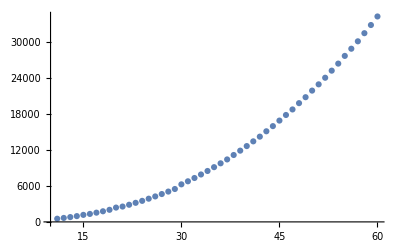

```mathematica
ListPlot[{Nlst,gTotalLst}ᵀ]
```

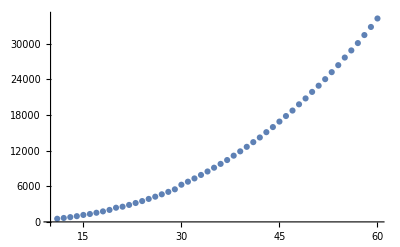

```mathematica
ListPlot[{Nlst,gTotalLstErr}ᵀ]
```

```mathematica
pres=4;presErr=1;
```

```mathematica
logFitLab=MaTeX[#,Magnification->1]&/@{"m="<>ToString[NumberForm[powLog,pres]]<>"\\pm"<>ToString[NumberForm[powLogErr,presErr]]}
```

{-Graphics-}

```mathematica
logFitLabRatio=MaTeX[#,Magnification->1]&/@{"m="<>ToString[NumberForm[powLogRatio,pres]]<>"\\pm"<>ToString[NumberForm[powLogErrRatio,presErr]]}
```

{-Graphics-}

```mathematica
dataLab=MaTeX[#,Magnification->1]&/@{"\\mathrm{data}"};
```

```mathematica
xyLab=MaTeX[#,Magnification->labMag]&/@{"\\log \\left( M \\right)","\\log \\langle N^{\\pm} \\rangle"}
```

{-Graphics-,-Graphics-}

```mathematica
xyLabRatio=MaTeX[#,Magnification->labMag]&/@{"\\log \\left( M \\right)","\\log \\langle N_n^{\\pm} \\rangle"}
```

{-Graphics-,-Graphics-}

```mathematica
legX=0.05;
```

```mathematica
capLoc={0.9,0.15}
```

{0.9,0.15}

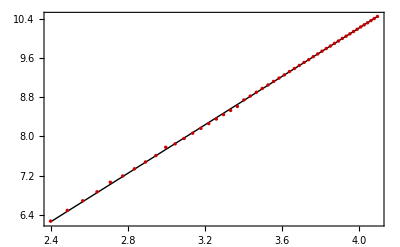

```mathematica
Show[{Plot[logFit[x],{x,Min[Log[Nlst]],Max[Log[Nlst]]},PlotStyle->{Black,dataThick},PlotLegends->Placed[LineLegend[logFitLab],{{legX-0.04,0.85},Right}]],ListPlot[{Log[Nlst],Log[gTotalLst]}ᵀ,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotStyle->darkRed,PlotLegends->Placed[LineLegend[dataLab],{{legX,0.72},Right}]],Graphics[Text[capTex⟦1⟧,Scaled[capLoc]]]},FrameLabel->xyLab,Frame->True,BaseStyle->texStyle,ImageSize->{Automatic,figW}]
```

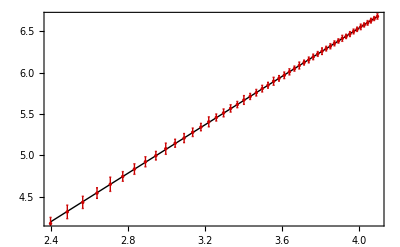

```mathematica
Show[{Plot[logFitRatio[x],{x,Min[Log[NRatiolst]],Max[Log[NRatiolst]]},PlotStyle->{Black,dataThick},PlotLegends->Placed[LineLegend[logFitLabRatio],{{legX-0.04,0.85},Right}]],ListPlot[{Log[Nlst],gRatioLogLstErr}ᵀ,PlotStyle->darkRed,(*IntervalMarkersStyle-><|"FenceWidth"->0.01|>,*)PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotLegends->Placed[LineLegend[dataLab],{{legX,0.72},Right}],IntervalMarkersStyle-><|"FenceWidth"->fenceW/2|>],Graphics[Text[capTex⟦2⟧,Scaled[capLoc]]]},FrameLabel->xyLabRatio,Frame->True,BaseStyle->texStyle,ImageSize->{Automatic,figW}]
```

```mathematica
Show[{Plot[logFit[x],{x,Min[Log[Nlst]],Max[Log[Nlst]]},PlotStyle->Orange,PlotLegends->Placed[LineLegend[logFitLab],{{legX-0.04,0.85},Right}]],ListPlot[{Log[Nlst],gLogLstErr}ᵀ,PlotLegends->Placed[LineLegend[dataLab],{{legX,0.75},Right}]]},FrameLabel->xyLab,Frame->{{True,False},{True,False}},BaseStyle->texStyle,ImageSize->{Automatic,6cm}]
```

```mathematica
theoLab=MaTeX[#,Magnification->1]&/@{"g=512M^{5/2}/135\\sqrt{3\\pi}"};
```

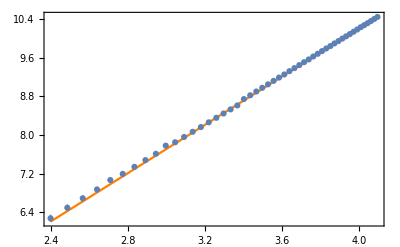

```mathematica
Show[{Plot[Log[512/(135 √(3π))]+5/2 x,{x,Min[Log[Nlst]],Max[Log[Nlst]]},PlotStyle->Orange,PlotLegends->Placed[LineLegend[theoLab],{0.25,0.85}]],ListPlot[{Log[Nlst],gLogLstErr}ᵀ,PlotLegends->Placed[LineLegend[dataLab],{0.17,0.75}]]},FrameLabel->xyLab,Frame->{{True,False},{True,False}},PlotRange->All]
```

```mathematica
CxyLab=MaTeX[#,Magnification->1.3]&/@{"\\log \\left( M \\right)","\\log \\left( C_{\\max} \\right)"}
```

{-Graphics-,-Graphics-}

```mathematica
colorLst
```

{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014],RGBColor[0.5238517042330579, 0.2719198391973829, 0.7153707394173552],RGBColor[0.37317160238437475, 0.63, 0.1550543242380685],RGBColor[0.7841372229535658, 0.23017255540928686, 0.26810462841072363],RGBColor[0.30841419880781473, 0.39995148071531117, 0.9],RGBColor[0.8969866052052705, 0.6599330260263523, 0.008136165945769741],RGBColor[0.6159549636873395, 0.252, 0.5408385174040933],RGBColor[0.01297068046342185, 0.6196234556292626, 0.6455648165561062],RGBColor[0.8378979015363919, 0.3644895076819594, 0.16083482646629865],RGBColor[0.469684000752239, 0.30351766622786064, 0.8507899981194027],RGBColor[0.5984511081857363, 0.6414945675761929, 0.],RGBColor[0.7164275936025443, 0.24371448127949116, 0.38095401066242623],RGBColor[0.19556481655611135, 0.4735481467551109, 0.8646777798673336],RGBColor[0.8744167287549299, 0.5470836437746498, 0.06907483236168915],RGBColor[0.5573291860767265, 0.2523913081219096, 0.6316770348081839],RGBColor[0.2197331439342194, 0.63, 0.35033963499281173],RGBColor[0.8153280250860514, 0.2516401254302569, 0.21274554230208187],RGBColor[0.3781589526487873, 0.35810462841072765, 0.9],RGBColor[0.8015799962388009, 0.6640644440265335, 0.],RGBColor[0.6522222356846489, 0.252, 0.4850427143313094],RGBColor[0.08271543430440877, 0.5638276525564729, 0.7292585211652906],RGBColor[0.8518468523045878, 0.4342342615229392, 0.128752239699448],RGBColor[0.5031614825959092, 0.2839891351523863, 0.767096293510227],RGBColor[0.46800178488796507, 0.63, 0.03436136468804449],RGBColor[0.7582744459071321, 0.2353451108185736, 0.3112092568214465],RGBColor[0.26530957039708464, 0.4258142577617492, 0.9],RGBColor[0.8883656795231258, 0.6168283976156295, 0.03141266528756009],RGBColor[0.5935405569137635, 0.252, 0.5753222201326715],RGBColor[0.06629468548404815, 0.63, 0.545624945747575],RGBColor[0.8292769758542473, 0.3213848792712366, 0.18066295553523118],RGBColor[0.44790370648976696, 0.3162577761061398, 0.9],RGBColor[0.6760394393250375, 0.6501154932583375, 0.],RGBColor[0.6905648165561062, 0.24888703668877876, 0.42405863907315633],RGBColor[0.1524601881453885, 0.5080318494836892, 0.8129522257744661],RGBColor[0.8657958030727825, 0.5039790153639124, 0.09235133170348728],RGBColor[0.5366389644395795, 0.26446060407691196, 0.6834025889010513],RGBColor[0.3145633264378097, 0.63, 0.2296466754427877],RGBColor[0.8001212982117243, 0.22697574035765516, 0.2414645029804596],RGBColor[0.33505432423806436, 0.3839674054571614, 0.9],RGBColor[0.8791683273781151, 0.6726853697086795, 0.],RGBColor[0.6298078289110768, 0.252, 0.519526417059882],RGBColor[0.039610805893685895, 0.5983113552850513, 0.677532967072423],RGBColor[0.8432259266224432, 0.39112963311221627, 0.14858036876838052],RGBColor[0.48247126095876225, 0.2960584311073887, 0.8188218476030944],RGBColor[0.5504988824112611, 0.6361665424901402, 0.],RGBColor[0.7324116688607027, 0.24051766622785947, 0.35431388523216223],RGBColor[0.22220494198636823, 0.4522360464109054, 0.8966459303836418],RGBColor[0.8797447538409784, 0.5737237692048922, 0.05468916462935822],RGBColor[0.571126150140184, 0.252, 0.6098059228612556],RGBColor[0.1611248679876543, 0.63, 0.42493198619753086],RGBColor[0.8206560501721027, 0.2782802508605137, 0.2004910846041637],RGBColor[0.40479907807904414, 0.34212055315257356, 0.9],RGBColor[0.7536277704643516, 0.6587364189404835, 0.],RGBColor[0.6660751009083862, 0.252, 0.46373061398709825],RGBColor[0.10935555973466561, 0.5425155522122675, 0.7612266716815987],RGBColor[0.8571748773906379, 0.4608743869531896, 0.11562783104527762],RGBColor[0.5159487428024325, 0.27652990003191436, 0.7351281429939188],RGBColor[0.4093935089414, 0.63, 0.10895371589276365],RGBColor[0.7742585211652906, 0.2321482957669419, 0.28456913139118245],RGBColor[0.29194969582734154, 0.4098301825035951, 0.9],RGBColor[0.8936937046091744, 0.6434685230458719, 0.01702699755522917],RGBColor[0.6073934221375008, 0.252, 0.5540101197884603],RGBColor[0.007686409537498939, 0.63, 0.620217296952274],RGBColor[0.8346050009402987, 0.34802500470149345, 0.16840849783731304],RGBColor[0.4617810393216153, 0.3081277270623911, 0.8705474016959619],RGBColor[0.6280872135505882, 0.6447874681722876, 0.],RGBColor[0.706548891814269, 0.2456902216371462, 0.39741851364288505],RGBColor[0.17910031357564535, 0.48671974913948374, 0.8449203762907744],RGBColor[0.8711238281588338, 0.5306191407941693, 0.07796566397114857],RGBColor[0.5494262246461028, 0.25700136895644005, 0.6514344383847431],RGBColor[0.2559550504912446, 0.63, 0.30423902664750685],RGBColor[0.8120351244899582, 0.23517562244979082, 0.22031921367309623],RGBColor[0.3616944496683212, 0.3679833301990073, 0.9],RGBColor[0.8312161016036528, 0.6673573446226281, 0.],RGBColor[0.6436606941348103, 0.252, 0.4982143167156765],RGBColor[0.06625093132394275, 0.5769992549408458, 0.7095011175887312],RGBColor[0.8485539517084946, 0.4177697585424731, 0.13632591107046238],RGBColor[0.49525852116528557, 0.2885991959869168, 0.7868536970867862],RGBColor[0.5025466566368246, 0.6308385174040916, 0.],RGBColor[0.7483957441188568, 0.23732085117622864, 0.3276737598019054],RGBColor[0.24884506741661863, 0.43569295955002885, 0.9],RGBColor[0.8850727789270298, 0.600363894635149, 0.04030349689701952],RGBColor[0.5849790153639175, 0.252, 0.5884938225170501],RGBColor[0.10251659204108926, 0.63, 0.49952433740225005],RGBColor[0.8259840752581541, 0.30492037629077057, 0.18823662690624554],RGBColor[0.431439203509301, 0.32613647789441946, 0.9]}

```mathematica
ClogFitLab=MaTeX[#,Magnification->1]&/@{"m="<>ToString[NumberForm[CpowLogEven,pres]]<>"\\pm"<>ToString[NumberForm[CpowLogErrEven,presErr]]}
```

{-Graphics-}

```mathematica
Ctitle=MaTeX[#,Magnification->1.3]&/@{"\\mathrm{even\,} M"};
```

```mathematica
{dataPlotEven,fitPlotEven}=plotLogFit[CFitModEven,NlstEven,CLogLstErrEven,CFitEntriesEven];
```

```mathematica
{dataPlotOdd,fitPlotOdd}=plotLogFit[CFitModOdd,NlstOdd,CLogLstErrOdd,CFitEntriesOdd,0.2];
```

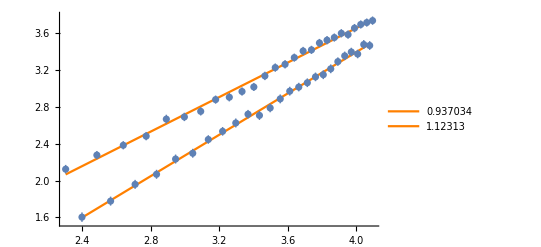

```mathematica
Show[dataPlotEven,fitPlotEven,dataPlotOdd,fitPlotOdd,PlotRange->All,AxesOrigin->{2.3,1.5}]
```

```mathematica
CdataLab=MaTeX[#,Magnification->1]&/@{"\\mathrm{even\,}M","\\mathrm{odd\,}M"};
```

```mathematica
ClogFitLab=MaTeX[#,Magnification->1]&/@{"m="<>ToString[NumberForm[CpowLogEven,pres]]<>"\\pm"<>ToString[NumberForm[CpowLogErrEven,presErr]],"m="<>ToString[NumberForm[CpowLogOdd,pres]]<>"\\pm"<>ToString[NumberForm[CpowLogErrOdd,presErr]]};
```

```mathematica
CdataLab
```

{-Graphics-,-Graphics-}

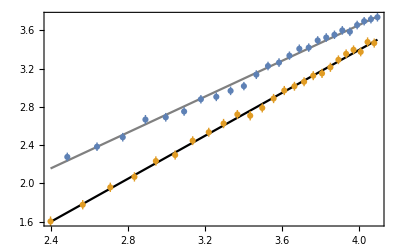

```mathematica
Show[{Plot[{CFitModEven[x],CFitModOdd[x]},{x,Min[Log[Nlst]],Max[Log[Nlst]]},PlotStyle->{Gray,Black},PlotLegends->Placed[LineLegend[ClogFitLab],{0.25,0.85}]],ListPlot[{{Log[NlstEven],CLogLstErrEven}ᵀ,{Log[NlstOdd],CLogLstErrOdd}ᵀ},PlotLegends->Placed[LineLegend[CdataLab],{0.85,0.25}]]},FrameLabel->xyLab,Frame->{{True,False},{True,False}}]
```

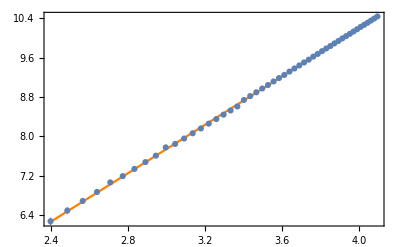

```mathematica
plotLogFit[logFit,Nlst,gLogLstErr,logFitLab,dataLab,xyLab]
```

## Plot 0.4

```mathematica
CxyLab=MaTeX[#,Magnification->labMag]&/@{"\\log \\left( M \\right)","\\log \\left[ \\left( \\Delta C^2 \\right) _{\\max} \\right]"}
```

{-Graphics-,-Graphics-}

```mathematica
CSumxyLab=MaTeX[#,Magnification->labMag]&/@{"\\log \\left( M \\right)","\\log \\langle \\left( \\Delta S_n \\right)^2 \\rangle)_{\\rm sat}"}
```

{-Graphics-,-Graphics-}

```mathematica
CSumxyLabOld=MaTeX[#,Magnification->labMag]&/@{"\\log \\left( M \\right)","\\log \\left[ \\left( \\Delta \\textstyle{\\sum}_{i=1}^n C_i \\right)^2 _{\\max} \\right]"}
```

{-Graphics-,-Graphics-}

```mathematica
presClog=2;
```

```mathematica
CpowLog04
```

0.994547

```mathematica
ClogFitLab=MaTeX[#,Magnification->labMag]&/@{"m="<>ToString[NumberForm[CpowLog04,presClog]]<>"\\pm"<>ToString[NumberForm[CpowLogErr04,presErr]]}
```

{-Graphics-}

```mathematica
CdataLab=MaTeX[#,Magnification->1]&/@{"\\mathrm{even\,}M","\\mathrm{odd\,}M"};
```

```mathematica
CLogLstErr04
```

{2.1230.023,1.9160.018,2.2460.019,2.1540.019,2.3360.016,2.3950.022,2.4470.016,2.4540.018,2.5130.018,2.5290.016,2.6320.022,2.6560.016,2.6820.018,2.7870.018,2.7540.016,2.8140.023,2.8480.016,2.8780.018,2.9150.019,2.9510.016,2.9680.023,3.0260.016,3.0500.018,3.0840.018,3.1030.016,3.1480.023,3.1610.016,3.1670.018,3.2120.019,3.2490.016,3.2380.022,3.2810.016,3.3080.019,3.3720.018,3.3870.016,3.3870.022,3.4180.016,3.4200.018,3.4300.019,3.4680.016,3.4940.022,3.4730.016,3.5250.019,3.5370.018,3.5650.016,3.6040.022,3.6140.016,3.5980.018,3.6250.018,3.6290.016,3.6780.022}

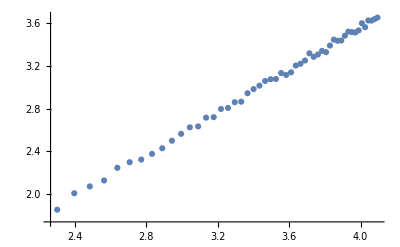

```mathematica
ListPlot[{Log[NlstC04],CLogLstErr04}ᵀ,PlotLegends->Placed[LineLegend[dataLab],{0.17,0.75}]]
```

```mathematica
Min[Log[NlstC04]]
```

Log[10]

```mathematica
Max[Log[NlstC04]]
```

Log[60]

```mathematica
Min[Log[NlstC04]]
```

```mathematica
Max[Log[NlstC04]]
```

```mathematica
CarLogLst04
```

{0.0288123,0.0159402,0.0219331,0.01933,0.0177495,0.0250428,0.0178157,0.0189071,0.0196512,0.016638,0.023318,0.0161095,0.0192659,0.0188751,0.0163905,0.0226155,0.0161475,0.0181003,0.0194769,0.0162451,0.0220879,0.0158964,0.0182591,0.0183811,0.0166418,0.022649,0.0165636,0.0188849,0.0189572,0.0162857,0.0217077,0.0159189,0.0191414,0.0191486,0.0159743,0.0235223,0.0164004,0.0178143,0.0184361,0.0161651,0.0224126,0.0158324,0.0193228,0.0189027,0.0163555,0.0222721,0.016531,0.0176906,0.0182805,0.0160691,0.0225984}

```mathematica
Plot[CarLogLst04[x],{x,Min[Log[NlstC04]],Max[Log[NlstC04]]},PlotStyle->Orange,PlotLegends->Placed[LineLegend[ClogFitLab],{0.25,0.85}]]
```

-Graphics-

```mathematica
CFitMod04
```

FittedModel[-0.187968+0.937229 x]

```mathematica
interc=CFitMod04["ParameterTableEntries"]⟦2,1⟧;
```

```mathematica
interc
```

-0.187968

```mathematica
5cm
```

141.732

```mathematica
Exp[interc]
```

0.828641

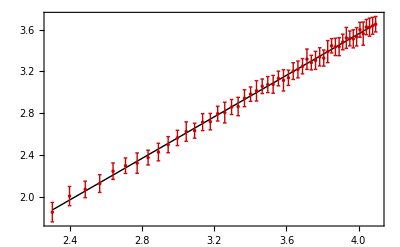

```mathematica
Show[{Plot[CFitMod04[x],{x,Min[Log[NlstC04]],Max[Log[NlstC04]]},PlotStyle->{Black,dataThick},PlotLegends->Placed[LineLegend[ClogFitLab],{{legX-0.04,0.85},Right}]],ListPlot[{Log[NlstC04],CLogLstErr04}ᵀ,PlotStyle->darkRed,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},PlotLegends->Placed[LineLegend[dataLab],{{legX,0.72},Right}],IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->fenceW|>],Graphics[Text[capTex⟦3⟧,Scaled[capLoc]]]},FrameLabel->CSumxyLab,Axes->None,Frame->True,PlotRange->All,ImageSize->{Automatic,figW},BaseStyle->texStyle]
```

```mathematica
{CarLogLst04,CLstErr04,CLogLstErr04,CdataLog04,CdataLogErr04,CFitMod04,CFitEntries04,CpowLog04,CpowLogErr04}
```

```mathematica
Dimensions[CLogLstErr04]
```

{51}

```mathematica
CLogLstErr04
```

{1.8510.013,2.0050.013,2.0700.011,2.1250.012,2.2440.011,2.2970.011,2.3210.014,2.3740.010,2.4270.012,2.4980.011,2.5630.010,2.6240.013,2.6320.010,2.7140.011,2.7190.011,2.7960.010,2.8060.014,2.8590.010,2.8640.012,2.9430.011,2.9820.010,3.0140.014,3.0580.010,3.0740.011,3.0770.012,3.1330.010,3.1150.014,3.1390.010,3.2030.011,3.2190.011,3.2500.010,3.3170.014,3.2850.010,3.3060.012,3.3400.012,3.3280.011,3.3900.015,3.4460.010,3.4350.012,3.4370.012,3.4830.011,3.5220.014,3.5160.010,3.5120.012,3.5320.012,3.6000.010,3.5630.016,3.6250.010,3.6240.012,3.6370.012,3.6530.011}

```mathematica
gTotalLstErr
```

{531.40.,661.44.,804.49.,965.54.,1172.60.,1332.65.,1541.69.,1771.75.,2017.80.,2388.86.,2562.91.,2859.96.,3183.101.,3510.107.,3872.114.,4249.120.,4648.128.,5059.130.,5488.135.,6265.141.,6775.147.,7324.151.,7913.160.,8495.166.,9131.172.,9772.179.,10421.186.,11161.191.,11887.197.,12649.204.,13438.206.,14223.215.,15117.222.,15979.229.,16903.238.,17836.241.,18761.245.,19811.254.,20803.262.,21904.269.,22947.275.,24051.282.,25233.289.,26409.294.,27694.302.,28893.311.,30129.312.,31483.322.,32846.331.,34274.341.}

## Misc test

```mathematica
ToString[powLogErr]
```

0.0512411

```mathematica
ToString[NumberForm[powLogErr,3]]<>"a"
```

0.0512a

```mathematica
Clear[b]
```

```mathematica
CLogLstErr04
```

{1.8510.013,2.0050.013,2.0700.011,2.1250.012,2.2440.011,2.2970.011,2.3210.014,2.3740.010,2.4270.012,2.4980.011,2.5630.010,2.6240.013,2.6320.010,2.7140.011,2.7190.011,2.7960.010,2.8060.014,2.8590.010,2.8640.012,2.9430.011,2.9820.010,3.0140.014,3.0580.010,3.0740.011,3.0770.012,3.1330.010,3.1150.014,3.1390.010,3.2030.011,3.2190.011,3.2500.010,3.3170.014,3.2850.010,3.3060.012,3.3400.012,3.3280.011,3.3900.015,3.4460.010,3.4350.012,3.4370.012,3.4830.011,3.5220.014,3.5160.010,3.5120.012,3.5320.012,3.6000.010,3.5630.016,3.6250.010,3.6240.012,3.6370.012,3.6530.011}

## GOE

```mathematica
mSzLst={10,15,20,25,30,35};
```

```mathematica
gLst={168.9,417.4,836,1204.75,1779.9,2421.8};
gLstErr={17.06,23.9,46.67,45.2,47.9,121.2};
```

```mathematica
gLstWithErr=makeDataErr[Log[gLst],gLstErr/gLst];
```

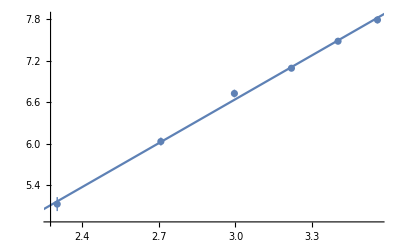

```mathematica
Show[ListPlot[{Log[mSzLst],gLstWithErr}ᵀ],Plot[goeMd["Function"][x],{x,Log[mSzLst⟦1⟧-1],Log[mSzLst⟦-1⟧+1]}]]
```

```mathematica
goeMd=LinearModelFit[{Log[mSzLst],Log[gLst]}ᵀ,x,x,]
```

FittedModel[0.290401+2.11861 x]